```mathematica
$HistoryLength=1;
```

```mathematica
a = Import["~/tmp/experiments/ComplexPExp1/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxm= Take[q, {1, Length[q], 100}];
lcomplexxm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/PseudoOptimalExp1/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxPm = Take[q, {1, Length[q], 100}];
lcomplexxPm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimpleJumpExp1/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxRm = Take[q, {1, Length[q], 100}];
lcomplexxRm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimplePRExp1/finalGrid.txt", "Table"];
q = Map[Mean, a];
exclusiveem = Take[q, {1, Length[q], 100}];
lexclusiveem = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimpleExp1/finalGrid.txt", "Table"];
q = Map[Mean, a];
optimallm = Take[q, {1, Length[q], 100}];
loptimallm  = Take[a, {1, Length[a], 100}];
```

```mathematica
rlcomplexxPm = lcomplexxPm[[2000]]
rlcomplexxRm = lcomplexxRm[[2000]]
rlcomplexxm = lcomplexxm[[2000]]
rlsimpleePm = lsimpleePm[[2000]]
rlsimpleeRm = lsimpleeRm[[2000]]
rlsimpleem = lsimpleem[[2000]]
rloptimallm = loptimallm[[2000]]
rlrandommm = lrandommm[[2000]]
rlrseannm = lseannm[[2000]]
rlexclusiveem = lexclusiveem[[2000]]
```

{3918.,3227.,4009.,4165.,3738.,3295.,3984.,3675.,3397.,3545.,3411.,3416.,3313.,3783.,3869.,3612.,4081.,3592.,3322.,3681.,3162.,3528.,3592.,3960.,3814.,3507.,3163.,3634.,3614.,3250.,3507.,3632.,3146.,3586.,3961.,4030.,3783.,3327.,3527.,3252.,3487.,3844.,3108.,3388.,3782.,3558.,3543.,3755.,3303.,3401.,3704.,3474.,3699.,3186.,4103.,3509.,3497.,3656.,3489.,3505.,3645.,3527.,3328.,3300.,4022.,3525.,3194.,3364.,3557.,3368.,3691.,3334.,3797.,3685.,3946.,3700.,3680.,3952.,3715.,3594.,3667.,3908.,3523.,3718.,3499.,3473.,3930.,3564.,3634.,3317.,3956.,3820.,3295.,3368.,3374.,3816.,3854.,3253.,3629.,3557.}

{3247.,3685.,3364.,3493.,3536.,3436.,3750.,3889.,3597.,3446.,3310.,3196.,4319.,3299.,3607.,3221.,3361.,3631.,3568.,3706.,3398.,3380.,3747.,3393.,4367.,3606.,3355.,4104.,3445.,3416.,3403.,3348.,3768.,3878.,3526.,3044.,3206.,3803.,3939.,3323.,3473.,3144.,3841.,3573.,3365.,3222.,3584.,3293.,3546.,3655.,4223.,3284.,4087.,3216.,3224.,3320.,3684.,3265.,3450.,3364.,3947.,3667.,3448.,4224.,3885.,3819.,3534.,3226.,3226.,3417.,3676.,3569.,3260.,3371.,3425.,3331.,3349.,3256.,2924.,3489.,3045.,3803.,3740.,3315.,3191.,3772.,3452.,3464.,3801.,3723.,3534.,3701.,3713.,3189.,3494.,3535.,3247.,3520.,3568.,3292.}

{4010.,3558.,3361.,3354.,3690.,3758.,3455.,3295.,3324.,3513.,3779.,3710.,3771.,3436.,3314.,3322.,3421.,3508.,3247.,3332.,3790.,3326.,3344.,3870.,3484.,3254.,3528.,3275.,3524.,3261.,3403.,3749.,3582.,3819.,3501.,3168.,3770.,3642.,3698.,3571.,3303.,3553.,3424.,3298.,3629.,3229.,3522.,3496.,3446.,3458.,3101.,3459.,3455.,3621.,3931.,3782.,3416.,3831.,3468.,3404.,3291.,3456.,3248.,3440.,3415.,3447.,3531.,3410.,3739.,3532.,3567.,3348.,3875.,3545.,3273.,3585.,3371.,3762.,3827.,3611.,3204.,3457.,3170.,4076.,3546.,3254.,3256.,3572.,3349.,3343.,3440.,3702.,3803.,3733.,3661.,3401.,3401.,3606.,3852.,3508.}

Part::partd: Part specification lsimpleePm ⟦ 2000 ⟧ is longer than depth of object.

lsimpleePm⟦2000⟧

Part::partd: Part specification lsimpleeRm ⟦ 2000 ⟧ is longer than depth of object.

lsimpleeRm⟦2000⟧

Part::partd: Part specification lsimpleem ⟦ 2000 ⟧ is longer than depth of object.

lsimpleem⟦2000⟧

{3318.,3628.,3484.,3605.,3656.,3625.,3674.,3589.,3920.,3622.,3413.,3864.,3524.,3647.,3423.,3408.,3687.,3493.,3205.,3548.,3361.,3777.,3315.,3611.,3508.,3133.,3604.,3615.,3831.,3145.,3412.,3379.,4052.,3465.,3264.,3516.,3416.,3413.,3223.,3408.,3657.,3170.,3614.,3552.,3666.,3743.,3328.,3859.,3115.,3700.,3394.,3620.,3603.,3671.,3659.,3743.,3302.,3277.,3183.,3318.,3769.,3537.,3473.,3470.,3758.,3569.,3287.,3654.,3483.,3539.,3606.,3483.,3292.,3281.,3655.,3739.,3701.,3087.,3899.,3171.,3441.,3751.,3263.,3432.,3332.,3717.,3287.,3180.,3379.,3610.,3479.,3597.,3295.,3526.,3411.,3307.,3259.,3588.,3611.,3574.}

Part::partd: Part specification lrandommm ⟦ 2000 ⟧ is longer than depth of object.

lrandommm⟦2000⟧

Part::partd: Part specification lseannm ⟦ 2000 ⟧ is longer than depth of object.

lseannm⟦2000⟧

{3172.,3507.,3314.,3382.,3462.,3283.,3580.,3547.,3417.,3271.,3349.,3294.,3374.,3945.,3419.,3391.,4063.,3754.,4081.,3616.,3567.,3559.,3375.,3650.,3662.,3306.,3519.,3442.,3391.,3410.,3297.,3302.,3223.,4125.,3245.,3285.,3759.,3666.,3321.,3226.,3111.,3383.,3464.,3180.,3410.,4220.,3317.,3389.,3187.,3258.,3673.,3568.,3584.,3661.,3548.,3891.,3340.,3508.,3315.,3285.,3873.,3310.,3836.,3630.,3706.,3521.,3568.,3595.,3188.,3569.,3449.,3279.,3792.,3558.,3470.,3685.,3028.,3560.,3400.,3637.,3658.,3205.,3962.,3378.,3568.,3474.,3716.,3509.,3205.,3563.,3647.,3383.,3243.,3212.,3548.,3318.,3653.,3578.,3597.,3858.}

```mathematica
alcomplexxPm = Map[Function[x, List[1,x]], rlcomplexxPm]
alcomplexxRm = Map[Function[x, List[2,x]], rlcomplexxRm]
alcomplexxm = Map[Function[x, List[3,x]], rlcomplexxm]
alsimpleePm = Map[Function[x, List[4,x]], rlsimpleePm]
alsimpleeRm = Map[Function[x, List[5,x]], rlsimpleeRm]
alsimpleem = Map[Function[x, List[6,x]], rlsimpleem]
aloptimallm = Map[Function[x, List[7,x]], rloptimallm]
alrandommm = Map[Function[x, List[8,x]], rlrandommm]

alseannm = Map[Function[x, List[9,x]], rlrseannm]
alexcluivem = Map[Function[x, List[10,x]], rlexclusiveem]
```

{{1,3918.},{1,3227.},{1,4009.},{1,4165.},{1,3738.},{1,3295.},{1,3984.},{1,3675.},{1,3397.},{1,3545.},{1,3411.},{1,3416.},{1,3313.},{1,3783.},{1,3869.},{1,3612.},{1,4081.},{1,3592.},{1,3322.},{1,3681.},{1,3162.},{1,3528.},{1,3592.},{1,3960.},{1,3814.},{1,3507.},{1,3163.},{1,3634.},{1,3614.},{1,3250.},{1,3507.},{1,3632.},{1,3146.},{1,3586.},{1,3961.},{1,4030.},{1,3783.},{1,3327.},{1,3527.},{1,3252.},{1,3487.},{1,3844.},{1,3108.},{1,3388.},{1,3782.},{1,3558.},{1,3543.},{1,3755.},{1,3303.},{1,3401.},{1,3704.},{1,3474.},{1,3699.},{1,3186.},{1,4103.},{1,3509.},{1,3497.},{1,3656.},{1,3489.},{1,3505.},{1,3645.},{1,3527.},{1,3328.},{1,3300.},{1,4022.},{1,3525.},{1,3194.},{1,3364.},{1,3557.},{1,3368.},{1,3691.},{1,3334.},{1,3797.},{1,3685.},{1,3946.},{1,3700.},{1,3680.},{1,3952.},{1,3715.},{1,3594.},{1,3667.},{1,3908.},{1,3523.},{1,3718.},{1,3499.},{1,3473.},{1,3930.},{1,3564.},{1,3634.},{1,3317.},{1,3956.},{1,3820.},{1,3295.},{1,3368.},{1,3374.},{1,3816.},{1,3854.},{1,3253.},{1,3629.},{1,3557.}}

{{2,3247.},{2,3685.},{2,3364.},{2,3493.},{2,3536.},{2,3436.},{2,3750.},{2,3889.},{2,3597.},{2,3446.},{2,3310.},{2,3196.},{2,4319.},{2,3299.},{2,3607.},{2,3221.},{2,3361.},{2,3631.},{2,3568.},{2,3706.},{2,3398.},{2,3380.},{2,3747.},{2,3393.},{2,4367.},{2,3606.},{2,3355.},{2,4104.},{2,3445.},{2,3416.},{2,3403.},{2,3348.},{2,3768.},{2,3878.},{2,3526.},{2,3044.},{2,3206.},{2,3803.},{2,3939.},{2,3323.},{2,3473.},{2,3144.},{2,3841.},{2,3573.},{2,3365.},{2,3222.},{2,3584.},{2,3293.},{2,3546.},{2,3655.},{2,4223.},{2,3284.},{2,4087.},{2,3216.},{2,3224.},{2,3320.},{2,3684.},{2,3265.},{2,3450.},{2,3364.},{2,3947.},{2,3667.},{2,3448.},{2,4224.},{2,3885.},{2,3819.},{2,3534.},{2,3226.},{2,3226.},{2,3417.},{2,3676.},{2,3569.},{2,3260.},{2,3371.},{2,3425.},{2,3331.},{2,3349.},{2,3256.},{2,2924.},{2,3489.},{2,3045.},{2,3803.},{2,3740.},{2,3315.},{2,3191.},{2,3772.},{2,3452.},{2,3464.},{2,3801.},{2,3723.},{2,3534.},{2,3701.},{2,3713.},{2,3189.},{2,3494.},{2,3535.},{2,3247.},{2,3520.},{2,3568.},{2,3292.}}

{{3,4010.},{3,3558.},{3,3361.},{3,3354.},{3,3690.},{3,3758.},{3,3455.},{3,3295.},{3,3324.},{3,3513.},{3,3779.},{3,3710.},{3,3771.},{3,3436.},{3,3314.},{3,3322.},{3,3421.},{3,3508.},{3,3247.},{3,3332.},{3,3790.},{3,3326.},{3,3344.},{3,3870.},{3,3484.},{3,3254.},{3,3528.},{3,3275.},{3,3524.},{3,3261.},{3,3403.},{3,3749.},{3,3582.},{3,3819.},{3,3501.},{3,3168.},{3,3770.},{3,3642.},{3,3698.},{3,3571.},{3,3303.},{3,3553.},{3,3424.},{3,3298.},{3,3629.},{3,3229.},{3,3522.},{3,3496.},{3,3446.},{3,3458.},{3,3101.},{3,3459.},{3,3455.},{3,3621.},{3,3931.},{3,3782.},{3,3416.},{3,3831.},{3,3468.},{3,3404.},{3,3291.},{3,3456.},{3,3248.},{3,3440.},{3,3415.},{3,3447.},{3,3531.},{3,3410.},{3,3739.},{3,3532.},{3,3567.},{3,3348.},{3,3875.},{3,3545.},{3,3273.},{3,3585.},{3,3371.},{3,3762.},{3,3827.},{3,3611.},{3,3204.},{3,3457.},{3,3170.},{3,4076.},{3,3546.},{3,3254.},{3,3256.},{3,3572.},{3,3349.},{3,3343.},{3,3440.},{3,3702.},{3,3803.},{3,3733.},{3,3661.},{3,3401.},{3,3401.},{3,3606.},{3,3852.},{3,3508.}}

Part::partw: Part {4, 2000} of {4, lsimpleePm} does not exist.

{4,lsimpleePm}⟦{4,2000}⟧

Part::partw: Part {5, 2000} of {5, lsimpleeRm} does not exist.

{5,lsimpleeRm}⟦{5,2000}⟧

Part::partw: Part {6, 2000} of {6, lsimpleem} does not exist.

{6,lsimpleem}⟦{6,2000}⟧

{{7,3318.},{7,3628.},{7,3484.},{7,3605.},{7,3656.},{7,3625.},{7,3674.},{7,3589.},{7,3920.},{7,3622.},{7,3413.},{7,3864.},{7,3524.},{7,3647.},{7,3423.},{7,3408.},{7,3687.},{7,3493.},{7,3205.},{7,3548.},{7,3361.},{7,3777.},{7,3315.},{7,3611.},{7,3508.},{7,3133.},{7,3604.},{7,3615.},{7,3831.},{7,3145.},{7,3412.},{7,3379.},{7,4052.},{7,3465.},{7,3264.},{7,3516.},{7,3416.},{7,3413.},{7,3223.},{7,3408.},{7,3657.},{7,3170.},{7,3614.},{7,3552.},{7,3666.},{7,3743.},{7,3328.},{7,3859.},{7,3115.},{7,3700.},{7,3394.},{7,3620.},{7,3603.},{7,3671.},{7,3659.},{7,3743.},{7,3302.},{7,3277.},{7,3183.},{7,3318.},{7,3769.},{7,3537.},{7,3473.},{7,3470.},{7,3758.},{7,3569.},{7,3287.},{7,3654.},{7,3483.},{7,3539.},{7,3606.},{7,3483.},{7,3292.},{7,3281.},{7,3655.},{7,3739.},{7,3701.},{7,3087.},{7,3899.},{7,3171.},{7,3441.},{7,3751.},{7,3263.},{7,3432.},{7,3332.},{7,3717.},{7,3287.},{7,3180.},{7,3379.},{7,3610.},{7,3479.},{7,3597.},{7,3295.},{7,3526.},{7,3411.},{7,3307.},{7,3259.},{7,3588.},{7,3611.},{7,3574.}}

Part::partw: Part {8, 2000} of {8, lrandommm} does not exist.

{8,lrandommm}⟦{8,2000}⟧

Part::partw: Part {9, 2000} of {9, lseannm} does not exist.

{9,lseannm}⟦{9,2000}⟧

{{10,3172.},{10,3507.},{10,3314.},{10,3382.},{10,3462.},{10,3283.},{10,3580.},{10,3547.},{10,3417.},{10,3271.},{10,3349.},{10,3294.},{10,3374.},{10,3945.},{10,3419.},{10,3391.},{10,4063.},{10,3754.},{10,4081.},{10,3616.},{10,3567.},{10,3559.},{10,3375.},{10,3650.},{10,3662.},{10,3306.},{10,3519.},{10,3442.},{10,3391.},{10,3410.},{10,3297.},{10,3302.},{10,3223.},{10,4125.},{10,3245.},{10,3285.},{10,3759.},{10,3666.},{10,3321.},{10,3226.},{10,3111.},{10,3383.},{10,3464.},{10,3180.},{10,3410.},{10,4220.},{10,3317.},{10,3389.},{10,3187.},{10,3258.},{10,3673.},{10,3568.},{10,3584.},{10,3661.},{10,3548.},{10,3891.},{10,3340.},{10,3508.},{10,3315.},{10,3285.},{10,3873.},{10,3310.},{10,3836.},{10,3630.},{10,3706.},{10,3521.},{10,3568.},{10,3595.},{10,3188.},{10,3569.},{10,3449.},{10,3279.},{10,3792.},{10,3558.},{10,3470.},{10,3685.},{10,3028.},{10,3560.},{10,3400.},{10,3637.},{10,3658.},{10,3205.},{10,3962.},{10,3378.},{10,3568.},{10,3474.},{10,3716.},{10,3509.},{10,3205.},{10,3563.},{10,3647.},{10,3383.},{10,3243.},{10,3212.},{10,3548.},{10,3318.},{10,3653.},{10,3578.},{10,3597.},{10,3858.}}

```mathematica
Needs["ANOVA`"]

ANOVA[Join[alcomplexxRm,alcomplexxPm,alcomplexxm,aloptimallm,alexcluivem], PostTests->Tukey]
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 4 | 569386. | 142346. | 2.56521 | 0.0375587
Error | 495 | 2.74681×10^7 | 55491.1 |  | 
Total | 499 | 2.80375×10^7 |  |  | ,CellMeans→All | 3525.02
Model[1] | 3590.78
Model[2] | 3520.65
Model[3] | 3511.5
Model[7] | 3504.47
Model[10] | 3497.72,PostTests→{Model→Tukey | {1,10}}}

```mathematica
grandommm =  ListPlot[Take[randommm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[randommm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[randommm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0.3`], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.2`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[randommm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

```mathematica
gseannm =  ListPlot[Take[seannm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[seannm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[seannm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0.3`], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.2`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[seannm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

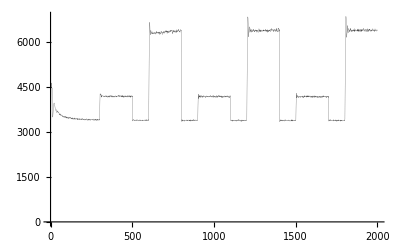

-Graphics-

```mathematica
goptimallm =  ListPlot[Take[optimallm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[« 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2031.38,3822.78,5229.86,6271.02,6906.23,7165.18,7221.32,7189.07,7096.01,6963.13,6875.4,6794.54,6494.58,6181.43,5947.16,5627.72,5161.52,4810.98,4589.84,4471.47,4329.78,4343.62,4330.23,4297.4,4266.21,4278.57,4322.97,4272.52,4378.69,4371.23,4351.73,4403.55,4448.23,4407.11,4394.52,4418.79,4482.98,4460.,4400.69,4417.82,4374.,4351.31,4287.17,4293.34,4299.17,4304.49,4245.21,4221.33,4145.61,4082.56,4101.25,4059.05,4035.9,3958.28,3952.18,3935.02,3913.46,3872.79,3822.65,3831.58,3802.73,3812.46,3777.2,3784.77,3760.3,3759.32,3728.02,3756.95,3720.4,3693.1,3695.81,3668.,3642.34,3645.54,3633.23,3630.49,3622.9,3570.87,3605.53,3591.64,3571.52,3565.9,3566.13,3554.23,3594.18,3579.75,3597.59,3544.71,3534.67,3563.,3530.75,3512.35,3561.24,3507.05,3513.74,3539.25,3526.01,3531.64,3534.36,3512.73,3547.06,3547.55,3502.56,3524.48,3512.52,3537.92,3490.99,3507.69,3517.14,3487.65,3457.64,3488.99,3526.67,3490.61,3504.56,3479.21,3498.11,3516.49,3493.27,3517.25,3492.92,3505.72,3468.83,3479.67,3513.59,3461.15,3475.16,3501.64,3499.81,3482.9,3517.76,3496.44,3498.56,3489.46,3477.03,3472.97,3477.13,3506.06,3511.83,3507.17,3498.62,3476.63,3469.92,3479.47,3487.57,3486.04,3483.2,3508.17,3493.24,3495.15,3470.86,3461.,3466.05,3473.94,3500.28,3510.61,3493.05,3485.17,3464.32,3491.53,3487.25,3492.12,3502.54,3486.03,3489.16,3481.07,3494.24,3497.22,3474.23,3460.3,3487.2,3474.82,3506.8,3461.32,3470.58,3466.84,3477.89,3484.91,3483.85,3471.2,3445.16,3462.17,3494.6,3459.71,3506.9,3505.99,3507.43,3453.64,3509.24,3467.66,3444.15,3452.53,3450.97,3462.95,3446.88,3462.46,3450.82,3466.68,3478.16,3465.07,3473.85,3478.51,3492.34,3471.9,3486.36,3497.43,3421.5,3449.18,3471.55,3457.01,3483.51,3442.39,3435.14,3431.11,3481.35,3488.13,3466.97,3434.65,3441.94,3439.46,3480.38,3463.43,3453.63,3442.87,3472.6,3448.27,3448.04,3472.8,3460.49,3459.73,3446.77,3462.51,3463.39,3432.67,3450.76,3454.36,3473.93,3485.19,3452.79,3476.67,3501.9,3457.86,3440.85,3491.93,3488.43,3463.32,3443.09,3475.57,3445.24,3471.48,3446.46,3448.32,3464.65,3459.49,3460.47,3482.07,3453.32,3468.81,3435.68,3514.59,3448.7,3459.85,3475.86,3469.19,3448.79,3475.3,3436.82,3475.26,3437.9,3446.7,3460.07,3439.8,3457.57,3453.25,3455.6,3455.53,3456.12,3441.16,3449.73,3465.76,3486.93,3464.45,3456.87,3441.27,3456.31,3473.5,3468.22,3464.79,3454.76,3472.3,3441.4,3480.25,3473.27,3455.79,3432.6,3437.36,3476.79,3483.59,3473.45,3462.12,3459.35,3445.92,3417.9,3444.9,3492.49,3426.62,3432.66,3473.84,3430.03,3448.08,3439.14,3445.36,3443.8,3433.44,3434.47,3432.74,3470.09,3461.49,3481.,3458.64,3462.55,3488.56,3460.53,3457.85,3468.87,3449.64,3480.15,3445.38,3467.82,3445.09,3436.95,3460.35,3458.02,3459.59,3474.12,3467.57,3426.32,3447.54,3449.16,3456.26,3461.21,3423.92,3469.5,3477.03,3448.06,3433.73,3445.87,3450.17,3450.47,3429.64,3465.,3446.73,3455.71,3443.14,3466.34,3437.84,3456.91,3464.82,3406.87,3443.05,3440.19,3442.95,3450.58,3445.77,3451.03,3468.18,3455.74,3456.5,3477.16,3440.81,3442.26,3479.86,3448.13,3441.52,3452.8,3429.69,3439.29,3464.82,3449.78,3477.03,3453.92,3437.88,3439.49,3428.42,3460.63,3499.12,3430.15,3436.63,3446.81,3462.37,3462.73,3439.02,3484.42,3453.24,3428.91,3455.92,3436.41,3431.21,3460.78,3416.23,3454.55,3460.33,3456.22,3454.62,3472.01,3424.71,3458.33,3457.92,3448.72,3439.65,3465.53,3460.58,3449.41,3443.59,3462.3,3444.62,3471.95,3461.51,3466.27,3472.87,3454.63,3456.03,3400.47,3451.9,3429.82,3419.86,3450.69,3432.88,3432.07,3467.92,3475.57,3431.14,3444.42,3441.63,3470.77,3440.83,3459.22,3437.23,3411.86,3452.61,3428.66,3435.46,3442.96,3415.88,3443.95,3455.31,3462.53,3469.78,3453.22,3429.73,3469.59,3442.85,3441.75,3466.49,3476.23,3451.1,3437.77,3443.96,3460.82,3424.03,3405.27,3427.98,3452.9,3450.83,3443.99,3444.09,3440.05,3457.76,3465.06,3449.81,3441.78,3468.73,3482.42,3448.83,3432.42,3461.51,3462.32,3473.99,3437.07,3441.32,3423.11,3424.64,3429.23,3440.42,3444.95,3452.4,3447.36,3421.62,3437.44,3461.48,3459.16,3439.5,3466.52,3439.,3461.25,3457.99,3464.79,3458.99,3433.09,3446.23,3459.06,3456.93,3430.96,3460.74,3482.95,3457.19,3434.93,3439.67,3456.9,3472.3,3441.1,3434.19,3460.63,3477.75,3462.16,3461.51,3444.09,3432.35,3412.01,3436.34,3457.46,3458.25,3460.88,3456.53,3430.04,3408.74,3458.24,3462.46,3464.43,3456.62,3420.31,3451.26,3445.79,3448.64,3408.19,3440.84,3454.99,3453.86,3415.18,3440.1,3444.66,3443.41,3435.32,3434.97,3459.29,3439.21,3450.07,3429.72,3428.96,3426.36,3431.15,3413.24,3438.33,3450.8,3455.02,3419.91,3473.02,3471.8,3453.45,3431.69,3457.17,3442.96,3458.82,3458.71,3402.41,3459.91,3450.33,3434.33,3430.41,3458.58,3439.28,3423.84,3422.08,3437.28,3452.82,3460.15,3449.9,3450.7,3463.19,3441.3,3474.83,3451.75,3446.83,3431.59,3455.11,3451.68,3431.8,3427.11,3437.81,3477.84,3436.35,3440.89,3423.47,3473.09,3448.86,3437.9,3450.17,3427.32,3446.38,3463.67,3453.33,3441.19,3438.56,3415.64,3424.07,3454.13,3417.36,3471.98,3477.55,3444.7,3419.79,3455.36,3434.99,3421.53,3462.05,3432.75,3445.49,3451.3,3449.57,3438.44,3432.25,3433.66,3434.26,3438.03,3456.09,3457.78,3476.39,3425.7,3461.62,3443.59,3449.1,3446.61,3450.85,3434.83,3399.87,3424.98,3431.25,3453.92,3441.66,3425.16,3444.7,3454.54,3427.98,3440.72,3458.49,3459.18,3429.6,3418.66,3449.16,3439.54,3444.38,3440.71,3446.44,3478.49,3421.72,3438.4,3466.26,3450.55,3438.67,3438.59,3431.32,3449.09,3437.87,3454.4,3468.13,3415.64,3461.61,3464.98,3449.34,3434.42,3451.23,3458.01,3446.89,3448.45,3456.73,3429.03,3465.14,3454.88,3423.22,3442.8,3454.79,3452.74,3420.77,3408.84,3443.21,3455.58,3449.03,3457.02,3433.16,3466.55,3464.62,3439.26,3442.9,3447.65,3434.89,3444.85,3465.37,3462.61,3452.8,3417.41,3429.7,3416.93,3456.47,3451.74,3450.02,3451.12,3454.59,3430.87,3454.94,3458.4,3459.29,3428.58,3437.19,3455.13,3451.26,3432.41,3438.85,3442.43,3450.38,3471.08,3456.9,3482.56,3482.08,3428.18,3454.59,3458.,3433.26,3445.23,3418.04,3439.08,3445.56,3472.47,3443.81,3429.82,3429.85,3448.48,3453.95,3450.47,3448.44,3457.98,3449.18,3438.45,3451.37,3461.47,3425.02,3442.14,3482.12,3445.43,3435.42,3471.41,3462.59,3456.2,3434.13,3464.73,3455.67,3449.21,3419.77,3459.6,3462.93,3434.77,3459.52,3423.85,3442.7,3464.14,3422.25,3459.79,3463.7,3429.65,3446.36,3446.8,3451.41,3475.76,3437.79,3450.16,3422.29,3456.69,3476.5,3470.85,3430.13,3441.51,3469.92,3443.84,3455.4,3447.37,3432.34,3469.39,3465.2,3435.62,3414.86,3423.17,3434.78,3443.71,3447.29,3417.99,3448.21,3440.13,3431.91,3445.04,3439.71,3449.36,3455.4,3434.,3442.3,3461.57,3429.7,3448.77,3452.46,3429.93,3435.9,3436.21,3471.17,3461.91,3453.97,3428.62,3411.9,3433.31,3478.18,3450.2,3441.57,3433.29,3459.99,3423.51,3413.29,3459.34,3440.97,3451.,3452.6,3444.3,3450.46,3441.01,3439.89,3442.37,3443.26,3422.84,3463.,3463.73,3418.92,3448.85,3412.37,3451.22,3460.33,3439.92,3428.99,3404.83,3411.49,3436.57,3450.51,3428.56,3447.93,3443.44,3461.01,3443.19,3412.66,3440.26,3420.34,3431.82,3433.58,3445.6,3457.24,3434.94,3437.5,3478.47,3424.85,3444.38,3423.32,3449.74,3438.08,3459.28,3429.65,3432.63,3446.21,3456.97,3460.87,3455.84,3449.48,3433.92,3460.06,3453.1,3423.8,3469.52,3463.98,3458.,3465.74,3434.12,3429.37,3457.97,3459.67,3473.78,3460.39,3448.45,3413.87,3442.85,3443.44,3471.94,3445.94,3420.28,3430.85,3439.48,3443.9,3413.25,3432.33,3443.26,3429.,3448.44,3443.86,3458.29,3451.05,3453.79,3469.16,3460.49,3450.86,3445.16,3419.25,3445.22,3424.99,3425.98,3441.07,3440.62,3453.74,3461.49,3434.52,3453.27,3453.79,3430.96,3435.8,3447.43,3448.16,3436.47,3476.19,3463.51,3462.86,3461.23,3433.75,3433.17,3446.29,3434.94,3436.77,3462.21,3442.09,3431.04,3434.14,3460.14,3453.19,3406.51,3429.27,3469.14,3466.01,3419.27,3437.48,3456.25,3438.14,3435.9,3426.65,3466.73,3459.07,3434.06,3436.12,3455.52,3471.47,3428.73,3443.62,3460.79,3441.21,3447.04,3435.32,3433.09,3469.01,3432.2,3441.98,3437.2,3426.81,3459.45,3432.18,3448.68,3425.37,3441.28,3468.84,3456.7,3451.1,3441.67,3437.53,3448.73,3425.41,3422.39,3432.38,3428.03,3445.18,3429.47,3425.74,3464.16,3438.48,3421.82,3457.63,3433.56,3471.86,3422.37,3423.39,3448.71,3446.28,3426.83,3433.08,3491.36,3421.52,3458.54,3478.16,3438.91,3456.03,3433.11,3447.89,3454.02,3455.09,3438.61,3432.38,3441.33,3432.87,3453.62,3465.55,3410.83,3443.19,3443.05,3455.25,3455.7,3443.18,3438.9,3428.86,3434.91,3445.75,3449.56,3429.15,3455.44,3425.29,3446.15,3446.6,3446.84,3427.94,3454.54,3431.18,3421.56,3460.82,3448.78,3403.09,3459.41,3420.19,3448.46,3449.3,3413.76,3447.72,3439.43,3439.58,3436.74,3442.81,3455.22,3439.91,3454.71,3481.09,3419.27,3427.18,3439.79,3438.49,3436.11,3427.48,3463.08,3436.88,3449.77,3412.73,3447.9,3451.14,3413.52,3433.64,3449.46,3455.71,3421.44,3433.25,3451.71,3436.81,3427.74,3422.82,3454.7,3462.79,3427.2,3455.79,3417.88,3445.11,3446.43,3455.89,3428.4,3492.05,3438.59,3445.62,3428.28,3438.33,3444.29,3436.,3446.55,3453.61,3440.7,3426.39,3427.38,3429.39,3438.45,3455.44,3424.,3426.23,3427.68,3462.64,3430.5,3456.62,3421.89,3451.63,3460.94,3434.69,3444.17,3476.82,3437.37,3470.44,3423.34,3438.85,3430.91,3445.03,3411.72,3450.6,3464.59,3410.51,3470.43,3437.12,3431.48,3441.86,3437.69,3442.55,3446.88,3443.89,3429.32,3438.26,3430.62,3461.52,3432.37,3451.52,3464.48,3450.28,3452.57,3464.61,3456.,3435.41,3449.05,3449.79,3449.59,3452.63,3466.44,3446.54,3438.6,3441.55,3424.65,3430.66,3425.66,3453.43,3419.01,3433.53,3432.87,3453.25,3446.06,3442.09,3451.62,3452.57,3424.7,3456.02,3442.65,3417.54,3468.43,3436.35,3428.58,3429.43,3456.24,3435.08,3439.3,3446.49,3441.28,3434.27,3424.27,3439.14,3415.79,3430.52,3463.79,3440.88,3422.02,3460.24,3437.75,3422.74,3443.64,3441.14,3427.5,3448.37,3464.21,3433.13,3471.52,3483.3,3451.38,3475.92,3422.51,3432.67,3460.26,3435.13,3453.11,3431.86,3470.39,3445.18,3443.8,3434.95,3467.26,3449.31,3446.21,3446.1,3448.96,3483.1,3423.34,3418.97,3433.26,3438.11,3473.54,3447.62,3436.49,3451.03,3450.45,3465.9,3422.71,3419.31,3441.85,3441.54,3438.83,3430.01,3405.75,3454.73,3457.08,3443.91,3446.15,3437.48,3453.22,3456.12,3452.45,3464.24,3421.29,3411.15,3452.54,3438.94,3458.23,3415.81,3423.42,3435.86,3433.25,3447.94,3455.51,3438.01,3457.44,3430.76,3434.33,3446.15,3424.62,3440.7,3418.41,3444.83,3457.58,3476.5,3464.34,3444.23,3438.05,3440.76,3430.02,3455.09,3446.75,3413.26,3447.83,3453.11,3440.8,3444.31,3458.14,3424.07,3456.78,3435.85,3440.74,3420.69,3419.08,3451.77,3435.18,3421.,3408.63,3442.16,3414.53,3437.79,3444.56,3431.85,3428.92,3437.71,3446.77,3423.51,3440.84,3419.15,3447.66,3417.88,3402.95,3457.2,3461.58,3442.32,3431.62,3432.88,3445.83,3441.34,3412.91,3451.26,3448.94,3454.54,3402.31,3423.15,3431.63,3422.21,3425.17,3459.48,3471.17,3452.99,3434.09,3419.98,3478.39,3468.43,3441.07,3462.48,3442.47,3446.93,3442.45,3458.54,3437.53,3423.57,3416.16,3452.55,3451.09,3446.77,3463.89,3477.07,3456.47,3465.11,3440.02,3442.24,3439.71,3455.14,3403.44,3414.61,3436.78,3484.11,3465.11,3429.1,3455.47,3445.66,3418.64,3399.2,3430.44,3469.35,3434.19,3440.69,3478.28,3427.94,3418.48,3440.78,3440.53,3428.62,3440.49,3432.53,3449.87,3431.65,3438.75,3436.72,3427.84,3432.91,3441.69,3467.04,3448.68,3473.7,3462.41,3451.31,3446.07,3460.63,3451.22,3464.09,3476.05,3432.96,3441.19,3422.64,3484.19,3455.1,3455.84,3454.43,3454.23,3417.24,3441.12,3467.88,3430.27,3424.97,3487.81,3462.48,3471.74,3419.49,3430.89,3435.88,3439.72,3422.82,3445.95,3456.11,3421.9,3440.93,3432.25,3458.88,3435.24,3446.89,3426.01,3396.81,3441.73,3455.11,3429.95,3450.37,3472.58,3430.54,3425.68,3423.18,3458.93,3397.23,3438.7,3465.04,3457.7,3440.54,3460.7,3452.54,3422.03,3446.98,3424.29,3431.38,3426.63,3446.34,3488.73,3482.21,3400.92,3432.79,3445.87,3431.33,3445.96,3445.59,3426.,3447.07,3472.15,3432.19,3460.28,3451.99,3422.08,3442.1,3439.12,3439.89,3433.33,3434.31,3450.22,3475.09,3466.28,3448.74,3437.63,3474.18,3444.23,3459.63,3436.18,3440.91,3426.55,3404.32,3431.52,3452.57,3440.19,3479.29,3435.94,3440.36,3462.79,3458.59,3456.66,3443.25,3458.51,3422.47,3417.48,3405.47,3429.44,3432.01,3475.93,3452.86,3407.66,3478.51,3471.95,3441.39,3453.95,3438.22,3456.19,3451.7,3425.79,3457.23,3440.52,3440.91,3449.79,3473.77,3449.15,3437.28,3427.08,3430.91,3467.53,3438.53,3435.15,3453.69,3429.85,3435.21,3439.15,3444.81,3452.44,3459.42,3436.57,3468.18,3445.15,3438.93,3426.51,3451.02,3460.55,3447.17,3448.28,3432.,3440.22,3439.1,3443.25,3433.05,3433.53,3452.4,3452.31,3451.24,3432.52,3435.25,3452.4,3416.28,3434.74,3448.4,3437.34,3450.23,3433.15,3432.09,3437.81,3421.89,3433.95,3404.99,3427.77,3408.68,3452.34,3432.38,3428.35,3446.03,3445.26,3412.44,3446.35,3402.76,3422.43,3423.69,3452.12,3468.73,3442.38,3418.21,3457.03,3443.27,3461.45,3415.48,3437.82,3433.77,3418.14,3450.11,3441.99,3451.98,3432.11,3437.4,3434.44,3405.73,3416.52,3438.98,3445.48,3398.27,3423.09,3478.35,3460.92,3412.8,3424.32,3432.87,3445.89,3453.43,3474.65,3420.32,3459.79,3429.31,3460.07,3479.27,3443.2,3448.26,3402.1,3456.35,3445.32,3422.23,3424.81,3430.02,3422.5,3413.06,3443.94,3451.31,3426.77,3441.1,3432.75,3434.14,3420.61,3410.69,3444.21,3457.58,3436.57,3429.14,3451.14,3411.43,3427.12,3446.87,3431.1,3425.72,3436.21,3424.19,3421.43,3449.41,3432.4,3454.27,3442.95,3437.63,3463.83,3423.34,3424.3,3449.69,3459.23,3438.59,3414.81,3447.51,3429.99,3449.95,3429.45,3440.56,3451.7,3423.78,3437.39,3436.7,3447.84,3444.29,3445.75,3448.56,3442.51,3465.64,3451.08,3409.2,3423.,3431.42,3443.15,3444.81,3442.,3449.82,3454.3,3473.96,3460.74,3427.55,3408.3,3424.96,3430.99,3424.62,3447.42,3458.11,3443.06,3437.84,3419.2,3453.27,3438.89,3456.68,3438.32,3431.48,3425.86,3420.71,3483.57,3464.82,3429.73,3421.17,3468.64,3451.97,3451.57,3442.03,3454.22,3427.83,3438.37,3462.32,3401.68,3425.88,3460.63,3452.59,3427.32,3441.41,3435.41,3416.55,3430.16,3433.77,3410.28,3422.75,3445.22,3449.77,3448.9,3440.03,3444.58,3424.56,3418.49,3426.03,3441.97,3435.08,3441.37,3449.91,3452.01,3410.02,3429.95,3443.1,3442.56,3424.22,3450.72,3434.14,3416.03,3473.03,3408.42,3466.27,3432.63,3444.63,3445.2,3461.08,3429.24,3445.18,3421.37,3440.06,3418.36,3433.66,3433.38,3432.01,3457.12,3419.91,3439.44,3424.75,3460.8,3434.35,3451.47,3432.58,3438.27,3462.41,3438.74,3432.93,3407.87,3456.45,3452.62,3419.82,3446.28,3453.63,3437.81,3443.33,3465.31,3437.28,3441.51,3403.86,3466.8,3443.9,3429.14,3427.3,3433.47,3463.44,3446.,3426.86,3431.44,3448.28,3456.61,3477.7,3444.52,3470.39,3426.71,3407.9,3449.19,3426.01,3450.77,3443.18,3429.01,3435.25,3443.07,3431.53,3433.03,3441.35,3470.99,3442.14,3424.44,3441.16,3413.81,3430.46,3424.66,3452.42,3454.7,3425.,3459.86,3444.08,3469.28,3444.48,3448.47,3465.65,3444.26,3453.78,3443.82,3405.68,3440.89,3449.26,3452.94,3465.92,3470.3,3422.6,3441.03,3444.28,3462.81,3438.36,3409.8,3449.83,3430.39,3442.93,3440.63,3458.52,3427.05,3402.94,3425.14,3438.91,3429.47,3447.31,3443.39,3435.38,3492.05,3431.74,3439.57,3441.81,3442.64,3446.79,3413.47,3393.82,3432.67,3440.61,3439.91,3435.49,3427.59,3427.25,3474.06,3437.24,3455.89,3444.27,3446.29,3458.54,3412.66,3444.92,3434.,3418.99,3440.17,3445.85,3453.16,3394.28,3442.4,3461.92,3447.79,3436.53,3429.97,3464.21,3424.76,3430.43,3464.72,3435.33,3431.66,3456.69,3410.77,3455.62,3453.13,3429.62,3415.9,3445.53,3445.03,3471.89,3437.74,3408.25,3465.56,3458.71,3443.9,3417.98,3415.95,3438.68,3440.,3446.33,3428.78,3438.24,3425.57,3456.03,3434.22,3435.85,3440.68,3441.41,3483.45,3442.1,3456.88,3440.88,3450.25,3434.32,3424.63,3434.43,3451.12,3434.93,3438.4,3430.63,3435.78,3460.62,3443.61,3464.76,3447.23,3459.36,3433.71,3451.62,3420.63,3417.89,3430.17,3457.15,3432.38,3427.62,3459.04,3439.85,3414.01,3448.41,3432.18,3422.51,3432.19,3464.71,3469.12,3399.93,3414.98,3447.57,3444.15,3418.24,3455.85,3436.51,3461.89,3423.32,3422.11,3451.28,3478.41,3442.99,3452.94,3466.45,3436.03,3457.64,3465.67,3428.38,3416.54,3419.65,3435.44,3419.95,3453.22,3469.64,3441.79,3440.33,3433.38,3440.3,3439.77,3426.84,3423.56,3452.37,3427.65,3432.76,3430.32,3442.29,3461.58,3464.78,3427.97,3425.42,3445.99,3428.71,3449.13,3453.52,3404.05,3436.07,3443.26,3413.51,3441.76,3444.99,3431.01,3421.46,3439.36,3418.88,3450.26,3434.3,3430.5,3426.97,3445.16,3447.82,3426.69,3445.68,3424.53,3459.78,3450.5,3447.17,3504.47},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

```mathematica
gcomplexxPm = ListPlot[Take[complexxPm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Red, Thickness[0.001]}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2027.75, 3246.76, 3689.3, 3700.76, 3588.59, 3596.42, 3621.6, 3609.59, 3567.77, 3608.39, 3639.57, 3601.5, 3592.72, 3592.45, 3605.76, 3597.69, 3628.91, « 18 », 3637.39, 3617.24, 3604.64, 3605.35, 3606.27, 3642.95, 3640.61, 3633.43, 3621.43, 3606.83, 3621.26, 3621.95, 3591.51, 3630.66, 3613.44, « 1950 »}, « 2 », « 9 » → « 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2027.75,3246.76,3689.3,3700.76,3588.59,3596.42,3621.6,3609.59,3567.77,3608.39,3639.57,3601.5,3592.72,3592.45,3605.76,3597.69,3628.91,3611.97,3607.18,3624.13,3605.73,3615.42,3594.02,3604.89,3548.35,3629.32,3602.43,3618.28,3641.36,3609.9,3605.75,3595.02,3563.34,3605.44,3635.87,3637.39,3617.24,3604.64,3605.35,3606.27,3642.95,3640.61,3633.43,3621.43,3606.83,3621.26,3621.95,3591.51,3630.66,3613.44,3627.7,3594.93,3607.27,3606.64,3614.85,3597.65,3596.81,3600.53,3636.86,3600.79,3582.72,3620.13,3645.25,3637.27,3633.64,3628.19,3630.59,3624.44,3575.09,3622.64,3591.45,3633.41,3632.72,3585.6,3598.34,3617.09,3611.89,3628.07,3622.76,3601.37,3598.45,3605.03,3627.21,3605.26,3631.73,3576.85,3607.21,3623.19,3614.55,3586.2,3630.99,3644.8,3615.4,3623.15,3619.07,3644.19,3613.37,3602.38,3621.56,3606.07,3652.59,3613.13,3603.89,3626.47,3605.43,3620.26,3615.6,3615.99,3584.56,3627.71,3640.45,3598.66,3615.49,3606.06,3609.65,3634.89,3599.25,3626.77,3578.14,3564.05,3581.97,3598.13,3582.56,3650.17,3649.22,3612.73,3589.55,3622.71,3601.89,3606.82,3644.03,3592.94,3623.17,3623.95,3612.17,3599.04,3588.29,3610.02,3635.68,3646.25,3609.08,3592.06,3626.78,3602.17,3603.43,3624.6,3629.12,3627.54,3624.12,3646.95,3614.77,3613.63,3620.4,3592.91,3623.51,3587.77,3594.58,3614.63,3615.31,3638.45,3638.17,3588.64,3600.12,3625.43,3580.98,3588.06,3594.05,3604.77,3593.42,3618.,3603.38,3596.54,3609.13,3576.98,3581.89,3627.63,3628.74,3612.1,3624.97,3615.29,3622.56,3626.68,3614.17,3600.85,3612.74,3615.37,3593.78,3622.15,3592.33,3620.66,3618.83,3623.46,3593.46,3627.23,3603.66,3642.73,3631.16,3607.61,3602.29,3642.03,3594.88,3624.69,3632.4,3596.54,3640.51,3635.91,3630.87,3618.22,3582.38,3578.93,3625.08,3613.68,3612.21,3602.72,3621.64,3596.55,3618.99,3628.14,3609.49,3613.29,3631.68,3599.52,3637.31,3624.11,3619.93,3612.48,3590.1,3588.28,3613.75,3579.85,3600.71,3619.88,3585.18,3626.51,3613.36,3609.72,3590.77,3635.3,3631.87,3623.68,3611.99,3614.3,3595.49,3635.53,3603.94,3622.72,3601.54,3609.15,3615.87,3613.63,3592.57,3632.12,3587.14,3592.59,3631.52,3617.59,3614.22,3594.87,3619.17,3606.39,3598.44,3600.18,3600.16,3614.82,3612.08,3619.76,3619.79,3638.92,3589.87,3627.34,3633.18,3590.96,3576.51,3590.6,3619.7,3601.48,3637.36,3642.84,3632.34,3621.38,3614.65,3613.38,3635.1,3626.2,3640.37,3612.44,3602.63,3622.2,3619.73,3626.23,3605.86,3627.51,3615.34,3584.25,3607.76,3639.95,3624.88,3639.2,3620.05,3602.21,3662.89,3593.16,3570.52,3610.93,3618.71,3614.42,3626.17,3622.98,3564.13,3623.74,3649.69,3616.26,3627.84,3648.37,3623.31,3608.61,3579.9,3642.79,3619.42,3620.92,3616.74,3642.62,3604.79,3587.77,3615.45,3629.84,3619.86,3619.12,3601.08,3618.52,3589.88,3606.97,3616.77,3626.83,3612.32,3601.42,3570.05,3614.2,3620.38,3587.39,3591.83,3631.8,3637.71,3614.29,3636.56,3631.3,3617.16,3633.25,3602.46,3619.58,3602.64,3617.7,3604.53,3592.64,3631.02,3599.56,3589.57,3592.91,3613.65,3590.57,3586.15,3602.42,3603.11,3608.15,3636.33,3616.89,3624.21,3621.14,3603.47,3604.22,3609.69,3597.4,3645.05,3600.15,3605.78,3606.53,3577.01,3582.93,3660.33,3584.72,3578.45,3618.45,3625.97,3617.64,3581.81,3586.88,3594.83,3625.58,3623.91,3625.63,3577.98,3593.53,3583.41,3598.34,3591.2,3624.98,3574.96,3612.25,3630.83,3601.76,3602.38,3609.83,3633.33,3634.33,3583.46,3602.66,3615.3,3616.14,3640.3,3608.07,3609.69,3616.03,3590.68,3627.34,3630.58,3602.35,3585.89,3636.82,3642.96,3634.32,3620.69,3631.87,3621.75,3632.79,3600.92,3607.57,3635.58,3618.02,3627.,3601.88,3652.43,3601.65,3600.75,3619.55,3580.79,3594.69,3632.62,3604.27,3617.13,3630.26,3615.45,3644.54,3605.45,3602.49,3580.66,3631.17,3571.89,3605.02,3627.77,3624.39,3654.71,3621.36,3624.92,3613.34,3643.32,3609.29,3612.64,3606.8,3627.89,3615.25,3560.83,3609.86,3631.18,3593.68,3614.24,3626.63,3611.86,3637.92,3630.73,3590.88,3625.93,3611.16,3627.69,3600.52,3625.12,3628.78,3620.28,3622.21,3582.34,3616.06,3610.9,3629.67,3639.76,3606.2,3582.68,3605.21,3587.37,3597.1,3605.62,3654.04,3608.03,3643.76,3666.84,3575.78,3586.03,3592.27,3589.24,3588.82,3630.59,3605.71,3590.44,3617.24,3620.68,3618.02,3632.87,3619.62,3609.77,3593.9,3605.34,3608.73,3626.53,3649.47,3636.43,3582.76,3623.56,3586.72,3604.9,3607.94,3611.27,3622.04,3629.89,3611.07,3636.09,3611.64,3596.25,3597.79,3613.18,3611.17,3613.77,3592.33,3589.69,3622.8,3634.64,3633.84,3617.63,3605.68,3632.77,3609.2,3647.07,3626.58,3623.94,3619.94,3639.04,3636.56,3621.64,3600.42,3643.02,3633.74,3595.71,3595.98,3611.33,3611.7,3598.9,3632.45,3597.11,3608.06,3617.87,3592.25,3606.19,3634.83,3588.94,3597.91,3625.85,3616.63,3620.29,3620.85,3601.91,3585.73,3636.84,3609.17,3601.82,3606.43,3605.9,3635.62,3626.1,3598.63,3609.51,3577.46,3581.53,3615.79,3638.97,3605.53,3640.25,3621.35,3601.58,3605.42,3615.21,3615.62,3594.42,3623.47,3610.28,3606.07,3628.63,3595.56,3611.4,3629.64,3590.67,3620.21,3623.03,3598.85,3589.22,3605.2,3609.13,3598.97,3604.1,3595.65,3614.81,3613.08,3592.21,3608.45,3585.65,3618.79,3627.88,3632.29,3596.46,3644.1,3609.16,3607.44,3581.46,3633.16,3606.33,3603.91,3618.43,3618.61,3593.77,3618.94,3603.05,3592.37,3580.45,3608.19,3603.,3586.98,3610.07,3618.97,3613.46,3658.38,3637.85,3620.6,3619.15,3636.84,3601.84,3633.03,3633.65,3600.1,3611.52,3659.14,3606.45,3599.65,3608.13,3643.95,3614.24,3616.11,3603.5,3602.35,3611.24,3618.57,3628.71,3625.75,3651.73,3648.71,3628.,3585.67,3613.19,3594.36,3630.26,3602.19,3633.42,3607.01,3604.8,3621.07,3630.16,3575.3,3610.51,3595.52,3606.26,3600.68,3603.12,3619.22,3580.,3649.67,3578.44,3621.59,3613.34,3596.99,3582.32,3601.44,3612.62,3614.27,3565.3,3616.01,3601.67,3607.11,3597.61,3624.01,3631.76,3595.23,3620.12,3668.12,3583.93,3598.89,3648.12,3567.91,3607.48,3622.72,3598.32,3617.72,3611.95,3608.12,3597.45,3611.61,3630.95,3599.57,3609.6,3591.76,3628.76,3631.75,3643.12,3597.06,3615.63,3631.81,3599.82,3614.59,3582.85,3582.,3586.82,3576.43,3644.62,3616.46,3583.37,3621.67,3600.76,3609.6,3609.02,3599.05,3575.46,3568.42,3589.54,3612.49,3603.91,3574.55,3591.98,3604.19,3593.02,3614.36,3606.74,3620.52,3654.39,3568.77,3604.,3607.28,3609.57,3627.55,3608.49,3609.92,3588.36,3624.88,3616.03,3600.01,3594.79,3588.73,3569.46,3597.33,3607.27,3573.25,3605.75,3610.3,3613.4,3607.68,3612.44,3646.79,3632.09,3603.2,3631.42,3636.6,3621.51,3604.42,3609.59,3562.98,3618.6,3641.8,3635.88,3615.79,3586.1,3606.25,3580.13,3608.69,3606.59,3612.98,3602.01,3608.3,3591.24,3587.58,3616.69,3590.71,3626.8,3602.58,3624.74,3605.92,3628.34,3633.51,3623.96,3616.88,3612.01,3653.19,3610.62,3627.59,3632.81,3639.9,3646.01,3626.84,3616.54,3608.28,3609.25,3573.63,3647.21,3586.46,3578.42,3595.77,3622.58,3587.42,3584.86,3626.58,3606.01,3633.95,3632.46,3631.91,3658.5,3638.95,3633.27,3606.67,3616.65,3592.97,3622.41,3605.13,3597.56,3608.18,3626.18,3608.54,3628.64,3618.28,3606.09,3621.71,3608.83,3584.42,3586.85,3586.2,3595.78,3602.35,3607.7,3627.89,3622.37,3590.67,3603.11,3594.73,3620.03,3597.44,3582.06,3620.65,3616.49,3617.3,3610.78,3620.36,3608.23,3600.11,3616.4,3600.22,3617.04,3645.82,3617.19,3618.65,3594.43,3614.28,3614.71,3614.99,3575.39,3659.35,3628.41,3622.98,3620.27,3650.01,3612.2,3607.6,3624.57,3614.19,3619.94,3587.66,3625.02,3604.21,3608.85,3594.44,3615.39,3609.59,3652.14,3614.66,3577.61,3592.58,3591.91,3611.08,3593.59,3618.59,3602.02,3592.34,3605.28,3609.92,3599.2,3587.62,3640.2,3559.89,3605.64,3632.92,3600.38,3601.65,3618.26,3609.17,3617.56,3609.97,3614.63,3605.87,3614.76,3614.32,3607.04,3610.65,3608.47,3639.2,3583.58,3597.47,3635.55,3611.16,3590.49,3621.71,3608.5,3615.62,3620.09,3616.46,3572.26,3592.19,3595.4,3552.26,3624.82,3588.09,3613.84,3618.1,3649.13,3606.48,3557.47,3588.89,3606.96,3622.06,3595.17,3573.54,3642.51,3613.83,3581.78,3595.9,3619.77,3613.44,3610.15,3637.56,3587.04,3660.66,3618.12,3568.42,3588.22,3597.46,3594.7,3575.47,3601.48,3600.23,3617.28,3619.41,3600.99,3584.85,3574.38,3599.02,3627.57,3622.59,3649.17,3589.21,3610.39,3633.59,3598.95,3609.86,3611.84,3632.58,3623.48,3594.44,3579.47,3629.49,3614.55,3621.18,3600.59,3600.88,3627.75,3624.34,3611.89,3625.36,3604.54,3644.8,3620.2,3596.17,3610.96,3647.08,3615.02,3620.35,3622.02,3597.35,3584.2,3603.2,3627.1,3627.67,3648.35,3642.85,3604.08,3596.26,3607.26,3622.28,3613.7,3584.88,3611.75,3615.56,3605.26,3627.5,3656.94,3604.04,3592.34,3607.14,3629.04,3596.97,3611.57,3621.74,3580.07,3578.18,3596.56,3650.93,3627.36,3605.02,3603.49,3611.07,3605.3,3615.7,3612.11,3639.72,3578.43,3647.02,3644.91,3634.71,3616.2,3619.56,3626.5,3601.46,3621.89,3640.52,3615.58,3620.9,3594.47,3589.94,3630.12,3637.49,3624.64,3608.78,3629.62,3604.64,3605.29,3624.66,3616.6,3608.69,3592.25,3648.98,3636.94,3589.34,3608.45,3605.24,3612.46,3603.92,3593.98,3626.62,3613.05,3601.61,3620.66,3606.78,3622.99,3608.37,3608.93,3585.29,3564.63,3629.55,3583.45,3603.92,3585.71,3571.01,3629.36,3605.4,3640.94,3629.28,3605.07,3589.88,3612.05,3573.34,3584.59,3591.93,3623.56,3640.9,3604.32,3628.26,3602.4,3630.02,3609.07,3634.,3593.94,3599.41,3643.95,3609.12,3570.78,3599.84,3604.2,3593.95,3654.48,3620.82,3624.41,3634.72,3583.84,3589.4,3576.67,3566.5,3584.11,3598.64,3613.67,3600.39,3598.77,3614.9,3603.64,3605.61,3606.98,3597.8,3608.54,3607.15,3595.96,3602.31,3622.07,3627.18,3617.61,3656.06,3620.35,3612.06,3603.89,3630.64,3589.93,3630.71,3573.7,3556.9,3585.44,3573.04,3619.25,3616.78,3619.22,3625.59,3602.38,3609.29,3590.75,3607.33,3608.13,3580.91,3622.37,3628.68,3628.72,3604.52,3614.85,3607.05,3624.27,3622.37,3586.27,3633.71,3574.8,3605.44,3596.07,3602.75,3630.36,3629.67,3592.76,3617.03,3593.3,3605.01,3603.85,3581.34,3645.16,3606.89,3581.04,3625.6,3607.79,3624.29,3631.37,3648.16,3611.67,3610.31,3600.86,3587.75,3640.35,3616.27,3593.42,3617.38,3607.74,3610.2,3596.34,3605.65,3603.97,3605.47,3607.49,3598.44,3633.64,3592.97,3580.91,3608.2,3630.67,3634.52,3598.32,3589.76,3607.94,3568.91,3602.57,3603.1,3593.4,3586.33,3643.36,3570.8,3618.82,3594.71,3601.15,3629.29,3587.85,3615.28,3614.49,3615.11,3619.07,3609.51,3597.17,3633.87,3604.91,3599.37,3601.63,3618.77,3606.3,3596.53,3651.05,3639.69,3632.98,3620.12,3615.14,3596.88,3639.16,3619.38,3598.8,3574.84,3595.59,3598.68,3637.79,3632.74,3602.45,3601.95,3601.67,3615.07,3617.63,3617.71,3622.47,3635.56,3625.44,3607.89,3592.25,3630.1,3632.95,3605.13,3614.76,3642.,3644.12,3602.64,3585.,3597.41,3563.4,3595.53,3621.73,3564.09,3647.,3613.65,3613.19,3634.,3623.14,3595.88,3629.38,3642.58,3600.97,3623.49,3630.28,3616.19,3627.7,3602.78,3592.2,3625.64,3608.78,3585.52,3615.29,3632.54,3599.82,3595.45,3600.92,3568.21,3599.28,3597.52,3620.75,3624.43,3624.04,3614.42,3582.8,3572.12,3600.49,3595.65,3592.66,3621.4,3626.26,3595.28,3602.1,3613.38,3596.46,3628.49,3629.36,3628.68,3631.54,3610.98,3602.13,3586.96,3615.88,3593.79,3624.87,3616.43,3630.85,3591.82,3576.34,3610.68,3602.46,3588.89,3633.09,3608.38,3580.49,3593.12,3581.42,3634.8,3635.01,3615.42,3622.39,3572.56,3645.14,3629.02,3613.62,3619.47,3622.34,3630.95,3597.46,3614.74,3617.38,3653.61,3641.8,3618.53,3639.,3637.43,3636.92,3604.7,3610.72,3624.01,3592.47,3605.53,3628.06,3624.06,3602.,3632.04,3606.85,3612.54,3581.03,3600.7,3614.87,3624.07,3621.46,3562.79,3598.1,3650.3,3606.5,3602.23,3592.03,3595.76,3588.66,3629.58,3601.8,3619.72,3594.71,3594.02,3616.35,3614.25,3619.27,3592.99,3605.33,3638.67,3628.49,3602.29,3647.16,3619.82,3616.5,3617.76,3622.96,3605.54,3678.51,3614.54,3585.43,3614.91,3613.56,3621.42,3617.69,3620.71,3617.62,3598.46,3622.15,3601.2,3600.94,3622.61,3607.23,3601.53,3637.92,3591.35,3599.04,3651.99,3606.96,3593.08,3615.58,3632.54,3615.15,3573.02,3628.4,3632.04,3590.01,3622.43,3608.27,3606.43,3594.12,3586.62,3601.69,3641.81,3596.81,3624.61,3593.86,3562.28,3621.89,3616.19,3621.86,3622.37,3601.33,3600.77,3599.81,3590.2,3606.49,3620.16,3656.42,3627.13,3623.45,3573.86,3634.29,3586.31,3665.04,3603.64,3597.94,3606.09,3627.5,3658.89,3613.02,3577.76,3592.9,3604.72,3600.52,3597.3,3580.89,3606.82,3629.88,3588.48,3601.18,3624.15,3617.51,3617.42,3609.79,3594.71,3633.,3621.33,3606.67,3639.29,3622.96,3604.51,3599.14,3635.06,3588.69,3608.92,3618.76,3614.79,3597.11,3578.83,3601.29,3604.37,3629.97,3608.91,3622.15,3629.13,3592.79,3597.82,3621.02,3588.32,3627.58,3598.6,3642.63,3586.43,3638.95,3619.61,3632.43,3588.94,3622.57,3618.38,3635.27,3610.22,3592.34,3612.03,3603.86,3618.73,3617.82,3636.33,3597.28,3605.35,3602.73,3638.97,3620.13,3613.95,3637.53,3621.23,3624.24,3593.55,3598.13,3613.,3606.14,3619.11,3605.56,3593.9,3610.74,3600.81,3624.24,3620.5,3619.79,3618.67,3626.44,3640.65,3601.93,3598.89,3617.09,3647.93,3616.39,3619.26,3610.,3605.79,3612.44,3610.85,3635.3,3633.74,3614.29,3611.62,3636.31,3612.57,3612.02,3568.12,3600.91,3616.35,3584.87,3609.27,3633.49,3588.76,3596.21,3621.42,3624.65,3604.15,3613.26,3588.5,3593.75,3622.69,3632.23,3617.62,3629.38,3596.82,3606.47,3598.03,3604.87,3587.72,3609.26,3629.1,3622.93,3644.04,3614.13,3602.41,3609.13,3608.38,3621.49,3636.46,3614.49,3621.33,3609.82,3595.62,3609.62,3607.04,3613.85,3608.84,3619.3,3614.5,3621.16,3603.38,3619.12,3614.74,3590.22,3603.53,3609.53,3641.7,3606.92,3602.21,3603.45,3596.26,3625.89,3602.58,3615.69,3597.24,3631.75,3608.31,3625.45,3622.54,3588.46,3600.66,3640.7,3630.42,3625.58,3587.09,3608.36,3615.08,3593.36,3627.53,3617.79,3615.91,3631.32,3628.66,3654.5,3612.92,3612.97,3598.21,3609.67,3628.2,3602.86,3632.34,3624.26,3641.55,3594.24,3604.63,3593.61,3643.02,3627.58,3599.72,3643.15,3627.96,3594.79,3592.25,3604.36,3631.6,3616.32,3630.21,3603.44,3601.07,3599.89,3657.88,3633.32,3614.57,3598.37,3612.9,3617.57,3590.4,3610.8,3601.1,3608.08,3587.37,3640.11,3650.62,3599.79,3552.32,3592.56,3590.72,3600.5,3571.01,3641.97,3628.44,3602.85,3616.64,3639.69,3635.25,3637.71,3605.54,3644.1,3630.28,3635.32,3586.54,3595.22,3626.23,3616.71,3596.76,3659.46,3616.19,3651.91,3644.86,3621.84,3606.68,3605.41,3624.04,3571.21,3594.16,3602.3,3593.6,3594.4,3596.32,3588.14,3613.55,3616.56,3572.71,3578.74,3616.61,3581.22,3599.23,3627.27,3615.6,3609.83,3639.08,3646.98,3648.8,3619.,3610.05,3626.52,3630.79,3623.49,3595.43,3597.15,3629.68,3607.01,3620.71,3609.47,3628.19,3637.48,3596.14,3613.23,3614.35,3604.59,3605.48,3652.88,3627.35,3626.62,3610.12,3611.06,3635.55,3622.32,3637.78,3604.59,3620.02,3612.3,3574.26,3588.11,3605.2,3602.35,3618.42,3607.96,3620.09,3607.06,3570.7,3587.86,3613.56,3599.65,3613.47,3635.36,3601.78,3646.49,3638.97,3637.29,3622.27,3608.42,3598.42,3599.69,3599.37,3609.37,3594.25,3611.1,3609.84,3656.29,3612.66,3603.25,3600.05,3626.87,3620.84,3634.99,3612.84,3579.56,3577.32,3611.17,3597.26,3616.68,3617.74,3629.58,3606.1,3584.06,3618.75,3588.96,3624.09,3601.19,3638.78,3628.76,3598.3,3618.79,3608.09,3588.5,3618.87,3601.67,3590.77,3618.1,3611.66,3581.9,3615.41,3603.48,3625.01,3615.83,3610.95,3608.88,3607.78,3622.91,3620.73,3622.86,3606.95,3601.18,3608.18,3624.79,3594.98,3606.33,3594.64,3617.73,3570.77,3566.92,3604.11,3657.08,3598.26,3606.01,3602.91,3581.93,3633.99,3603.1,3567.8,3606.72,3610.57,3616.26,3582.23,3615.57,3631.27,3586.84,3603.36,3646.53,3594.21,3603.35,3610.27,3605.29,3596.65,3581.09,3616.92,3633.61,3650.43,3600.11,3637.64,3611.97,3597.21,3583.62,3615.56,3613.93,3650.31,3614.77,3613.63,3614.77,3603.07,3597.32,3594.63,3609.29,3630.76,3619.82,3587.91,3627.01,3616.19,3600.23,3606.4,3645.31,3613.4,3584.63,3563.04,3621.42,3583.38,3615.23,3615.69,3607.56,3619.57,3639.36,3614.67,3605.7,3598.64,3613.01,3628.9,3607.44,3626.97,3619.96,3632.54,3629.14,3568.93,3555.37,3595.69,3625.19,3618.56,3610.98,3609.34,3584.15,3612.08,3631.46,3595.02,3655.1,3597.38,3612.8,3613.41,3615.11,3623.62,3585.03,3619.02,3587.82,3623.25,3646.73,3610.21,3599.38,3609.12,3592.74,3614.99,3580.21,3618.51,3584.68,3622.62,3637.73,3638.44,3623.17,3634.37,3626.82,3622.33,3664.26,3623.1,3605.68,3640.27,3636.89,3632.02,3622.51,3601.5,3591.98,3595.64,3632.78,3624.79,3626.15,3635.29,3592.35,3609.77,3617.54,3636.31,3572.94,3609.9,3596.69,3628.76,3637.2,3619.08,3580.01,3597.35,3621.78,3622.9,3614.81,3610.25,3608.73,3614.86,3642.26,3600.43,3603.82,3606.56,3604.93,3630.42,3607.45,3627.36,3584.98,3636.47,3607.51,3607.82,3600.67,3602.29,3621.36,3616.05,3599.54,3590.78},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001]}]

```mathematica
gcomplexxRm= ListPlot[Take[complexxRm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001], Dashing->Small}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2029.78, 3821.91, 5147.84, 6070.83, 6519.05, 6087.63, 5212.89, 4734.95, 4352.74, 4182.14, 4076.72, 3994.84, 3929.1, 3921.05, 3820.31, 3836.38, 3804.13, 3814.26, 3720.85, « 14 », 3615.19, 3630.93, 3657.67, 3614.65, 3623.9, 3665.11, 3609.49, 3579.01, 3576.02, 3598.88, 3581.73, 3634.69, 3631.92, 3614.69, 3591.24, 3614.46, 3628.44, « 1950 »}, « 2 », « 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2029.78,3821.91,5147.84,6070.83,6519.05,6087.63,5212.89,4734.95,4352.74,4182.14,4076.72,3994.84,3929.1,3921.05,3820.31,3836.38,3804.13,3814.26,3720.85,3720.97,3720.85,3700.72,3678.88,3691.83,3665.53,3687.33,3713.36,3677.3,3678.5,3687.59,3626.22,3648.24,3615.08,3615.19,3630.93,3657.67,3614.65,3623.9,3665.11,3609.49,3579.01,3576.02,3598.88,3581.73,3634.69,3631.92,3614.69,3591.24,3614.46,3628.44,3626.86,3627.07,3630.36,3604.66,3588.97,3564.42,3566.8,3583.54,3591.5,3591.77,3554.78,3602.1,3586.72,3576.76,3563.8,3584.7,3597.4,3561.31,3578.49,3590.77,3588.16,3574.45,3532.49,3573.33,3550.01,3560.98,3549.14,3560.39,3549.65,3507.72,3544.14,3575.9,3553.85,3557.98,3572.93,3576.22,3538.65,3502.34,3535.65,3533.71,3532.56,3520.54,3500.97,3553.02,3536.35,3527.27,3517.1,3589.94,3515.51,3548.95,3563.48,3552.44,3497.89,3509.43,3576.01,3566.31,3577.11,3575.1,3513.35,3526.19,3533.98,3531.91,3542.54,3545.82,3523.66,3529.78,3567.86,3514.71,3497.85,3528.21,3512.04,3516.13,3533.35,3492.57,3494.66,3535.33,3486.54,3495.06,3521.46,3511.38,3510.72,3501.23,3513.27,3501.75,3510.47,3507.81,3520.24,3525.64,3504.1,3525.34,3494.1,3525.25,3537.91,3508.59,3522.41,3522.3,3526.41,3529.5,3525.01,3508.11,3543.56,3502.32,3500.51,3493.69,3491.39,3548.26,3501.11,3521.41,3517.51,3525.16,3526.44,3484.29,3525.87,3476.29,3504.05,3506.3,3505.44,3514.17,3544.79,3529.67,3509.57,3530.63,3539.15,3506.01,3543.5,3493.06,3481.43,3458.37,3538.73,3556.38,3506.17,3502.93,3508.8,3519.56,3522.6,3493.92,3503.21,3490.14,3521.07,3488.92,3478.78,3484.36,3514.59,3512.75,3481.63,3497.35,3458.89,3523.8,3518.12,3550.79,3495.12,3512.63,3544.98,3523.02,3501.42,3473.84,3530.23,3531.2,3505.32,3557.11,3524.36,3551.18,3512.06,3532.19,3529.09,3489.3,3498.1,3527.98,3462.63,3505.32,3490.81,3496.19,3511.92,3489.42,3489.62,3515.13,3537.08,3513.51,3538.84,3547.96,3496.76,3485.99,3480.9,3530.97,3486.31,3485.64,3493.43,3496.46,3513.72,3541.38,3504.48,3492.59,3521.59,3524.41,3518.84,3498.75,3519.15,3485.93,3504.36,3487.51,3537.05,3539.47,3473.21,3471.41,3457.33,3552.63,3513.75,3500.46,3522.94,3571.38,3526.44,3521.53,3541.65,3530.87,3546.13,3548.89,3518.6,3524.59,3526.94,3537.92,3516.24,3477.35,3531.17,3509.22,3563.6,3509.49,3501.9,3524.89,3501.23,3512.27,3505.64,3494.78,3567.08,3538.46,3508.57,3490.55,3555.86,3476.3,3504.57,3520.08,3533.2,3516.42,3537.26,3567.2,3574.47,3559.9,3521.75,3516.55,3559.86,3544.34,3540.91,3516.45,3553.48,3540.47,3551.22,3545.13,3532.67,3541.05,3533.89,3484.24,3500.02,3512.09,3483.79,3512.82,3533.88,3556.81,3544.64,3510.32,3511.47,3526.3,3546.02,3527.77,3501.23,3497.17,3509.79,3546.06,3506.99,3529.14,3469.73,3540.26,3525.43,3523.89,3510.26,3536.21,3561.47,3518.96,3500.32,3533.28,3514.88,3509.27,3490.76,3502.77,3505.11,3511.2,3548.12,3557.52,3534.77,3498.14,3526.18,3560.55,3524.26,3547.78,3533.71,3487.48,3495.63,3540.44,3515.79,3557.15,3535.09,3521.08,3509.5,3528.1,3519.07,3505.31,3549.37,3510.89,3555.45,3536.7,3519.32,3520.27,3521.54,3505.83,3494.77,3518.98,3504.15,3517.71,3505.79,3525.5,3481.17,3513.54,3503.91,3515.85,3515.19,3515.39,3539.02,3532.57,3515.27,3501.74,3568.39,3528.55,3522.64,3496.86,3500.81,3514.8,3532.94,3508.23,3480.9,3506.73,3557.08,3525.62,3521.88,3496.25,3508.98,3487.63,3504.39,3519.39,3489.72,3470.04,3483.19,3500.23,3523.41,3497.5,3492.53,3522.7,3489.33,3485.74,3490.93,3493.45,3499.77,3474.96,3489.84,3500.56,3479.87,3468.19,3545.55,3529.65,3538.98,3536.82,3521.51,3524.28,3552.99,3503.86,3512.12,3478.07,3514.3,3525.41,3554.61,3514.22,3553.53,3516.61,3487.31,3522.41,3514.53,3509.21,3531.83,3514.36,3548.09,3530.22,3539.11,3497.6,3502.17,3582.13,3491.96,3498.34,3500.05,3508.37,3500.19,3461.86,3497.75,3523.13,3478.03,3513.86,3508.86,3495.02,3495.65,3493.08,3474.11,3482.65,3533.62,3488.,3513.23,3505.57,3512.65,3499.26,3493.68,3500.91,3504.97,3492.52,3540.49,3554.48,3534.82,3488.62,3502.35,3507.69,3545.96,3495.3,3488.93,3501.93,3516.56,3481.77,3490.11,3518.5,3537.99,3533.77,3507.37,3520.43,3516.83,3509.4,3556.68,3490.31,3497.7,3487.66,3517.46,3516.05,3477.91,3506.55,3511.07,3514.2,3510.22,3496.9,3513.37,3500.46,3518.83,3552.25,3524.13,3481.01,3504.73,3542.6,3502.07,3522.85,3535.98,3516.45,3555.49,3480.7,3536.31,3511.15,3519.96,3491.84,3500.24,3501.21,3477.33,3488.69,3523.25,3479.16,3484.98,3474.01,3474.32,3499.21,3454.31,3451.69,3489.4,3507.88,3515.55,3496.03,3471.97,3520.87,3533.31,3474.17,3500.8,3493.06,3507.2,3462.42,3486.5,3509.68,3521.,3537.65,3499.3,3525.73,3545.24,3523.93,3516.59,3506.27,3499.65,3494.4,3478.6,3504.27,3543.8,3487.24,3491.88,3518.03,3485.12,3503.92,3534.84,3549.32,3525.44,3561.47,3502.59,3500.41,3469.41,3458.61,3471.97,3491.7,3471.5,3501.99,3505.22,3518.52,3492.23,3504.82,3467.83,3495.67,3492.04,3507.1,3490.22,3514.2,3517.47,3506.12,3486.38,3501.55,3510.33,3476.51,3487.06,3497.54,3522.24,3553.87,3501.31,3508.63,3493.51,3473.94,3550.05,3508.37,3478.45,3520.06,3508.36,3475.99,3468.07,3497.82,3495.78,3497.01,3473.03,3504.84,3490.67,3511.09,3511.85,3505.63,3486.44,3547.55,3513.71,3524.14,3502.02,3491.88,3526.38,3516.3,3515.6,3478.44,3495.85,3542.33,3512.74,3475.1,3548.22,3518.08,3554.54,3523.87,3503.04,3532.94,3546.13,3542.88,3569.16,3528.,3525.73,3512.48,3500.78,3520.74,3497.12,3522.04,3548.07,3532.96,3479.24,3503.64,3487.71,3473.25,3471.35,3511.76,3550.97,3529.34,3502.66,3542.6,3547.39,3525.11,3497.11,3459.86,3463.76,3509.08,3504.3,3520.85,3494.59,3485.62,3471.47,3502.09,3466.74,3464.52,3500.57,3478.29,3477.63,3483.83,3484.49,3480.52,3456.29,3469.35,3486.98,3475.94,3475.94,3485.11,3449.71,3483.44,3470.13,3476.95,3509.49,3456.62,3464.3,3476.61,3510.16,3483.97,3504.01,3483.13,3468.95,3533.86,3499.54,3473.33,3497.07,3542.67,3528.83,3525.05,3498.6,3511.25,3529.99,3569.14,3528.26,3511.43,3508.84,3514.21,3498.92,3511.02,3513.87,3515.21,3459.78,3494.49,3549.67,3505.29,3449.84,3474.13,3507.49,3533.17,3499.09,3465.9,3508.79,3484.85,3512.96,3470.,3481.88,3463.89,3491.75,3507.68,3465.86,3492.14,3526.69,3499.83,3513.61,3539.96,3533.25,3530.02,3544.24,3517.4,3527.48,3481.94,3492.73,3518.92,3509.39,3519.02,3548.96,3508.52,3488.57,3523.63,3523.63,3499.,3489.83,3497.19,3461.93,3443.83,3514.2,3512.6,3522.33,3584.87,3542.95,3507.16,3459.8,3497.35,3471.95,3514.62,3528.63,3509.93,3505.72,3476.22,3477.73,3466.28,3486.,3553.45,3580.32,3523.55,3521.61,3511.45,3508.32,3530.06,3553.5,3544.01,3504.57,3482.33,3501.7,3502.15,3508.71,3515.26,3539.3,3510.01,3536.73,3552.69,3533.08,3507.66,3533.81,3516.23,3525.76,3546.49,3496.3,3505.33,3527.77,3506.19,3531.71,3502.25,3507.45,3541.2,3562.05,3538.42,3528.63,3526.65,3536.66,3545.77,3535.93,3499.59,3518.94,3558.71,3536.62,3546.15,3511.61,3556.43,3517.87,3510.43,3493.24,3509.24,3498.38,3519.64,3524.83,3555.35,3494.11,3475.58,3476.94,3484.96,3470.17,3482.49,3486.79,3503.56,3520.32,3507.69,3478.86,3502.69,3458.7,3465.15,3510.02,3503.04,3518.56,3482.54,3469.04,3469.58,3495.76,3506.54,3492.54,3472.08,3499.76,3518.29,3512.9,3500.29,3489.58,3487.01,3523.23,3516.12,3493.49,3519.22,3533.48,3476.24,3491.75,3525.29,3515.02,3519.81,3508.23,3541.41,3506.29,3476.71,3508.03,3507.44,3483.46,3498.81,3530.29,3494.46,3492.04,3493.46,3476.04,3499.57,3511.99,3519.58,3506.19,3479.5,3504.22,3529.67,3512.54,3507.29,3535.61,3486.53,3460.21,3476.73,3510.29,3474.96,3481.1,3509.09,3543.68,3516.22,3512.04,3542.25,3505.23,3492.08,3483.44,3499.84,3478.18,3467.18,3472.96,3495.67,3491.99,3458.39,3501.95,3530.66,3488.9,3519.27,3541.52,3510.7,3502.06,3479.14,3491.96,3513.57,3488.66,3491.77,3470.43,3490.28,3443.95,3487.33,3452.97,3496.84,3519.46,3489.6,3476.14,3480.54,3537.45,3537.5,3479.44,3495.09,3490.55,3474.55,3473.94,3497.6,3464.64,3509.3,3527.64,3498.09,3464.51,3494.35,3456.81,3453.21,3483.05,3470.95,3467.41,3515.18,3489.37,3521.46,3526.33,3485.2,3507.76,3524.11,3529.94,3529.32,3473.85,3490.96,3483.26,3510.91,3521.23,3496.66,3547.09,3499.61,3519.42,3496.77,3487.05,3504.31,3508.28,3507.09,3455.1,3446.19,3481.07,3476.39,3483.71,3484.03,3478.24,3474.95,3481.67,3489.3,3472.84,3488.37,3482.26,3438.4,3467.38,3471.52,3464.98,3482.77,3503.37,3505.29,3500.27,3508.26,3474.57,3482.26,3490.88,3496.44,3538.3,3523.26,3510.23,3493.67,3526.37,3474.75,3516.56,3510.71,3538.03,3524.24,3496.83,3489.03,3537.08,3550.8,3563.34,3540.39,3504.07,3490.5,3506.44,3516.83,3495.8,3528.33,3523.18,3534.59,3503.36,3504.39,3541.75,3505.29,3477.3,3499.95,3499.44,3551.17,3481.44,3497.4,3506.07,3525.54,3524.42,3485.3,3469.75,3485.59,3492.75,3527.47,3569.62,3554.86,3538.67,3492.82,3524.02,3499.45,3522.11,3532.29,3538.21,3485.23,3468.38,3516.58,3534.41,3533.53,3528.06,3514.75,3528.67,3507.55,3497.49,3531.44,3533.95,3550.63,3523.7,3542.58,3551.08,3533.24,3539.4,3510.7,3511.93,3536.88,3525.61,3500.25,3498.93,3538.56,3537.03,3519.9,3489.88,3475.22,3521.99,3501.01,3517.79,3517.36,3479.42,3505.95,3532.06,3500.14,3514.73,3514.6,3510.01,3490.69,3515.02,3560.22,3529.78,3550.98,3536.34,3549.25,3522.3,3492.29,3572.18,3519.83,3514.85,3499.09,3481.91,3561.81,3523.48,3431.4,3514.87,3530.29,3520.58,3518.39,3512.03,3530.3,3488.45,3471.58,3519.07,3511.53,3469.61,3532.91,3457.82,3503.61,3516.92,3494.24,3478.58,3511.81,3520.88,3471.3,3482.58,3481.78,3478.24,3533.69,3539.25,3527.17,3544.71,3496.07,3465.1,3496.07,3491.38,3476.16,3511.14,3478.99,3468.14,3494.49,3465.57,3511.26,3485.73,3480.73,3505.28,3456.37,3498.43,3461.75,3482.19,3512.61,3502.86,3513.57,3453.79,3497.13,3477.82,3512.64,3515.75,3493.47,3515.46,3496.07,3517.85,3504.1,3502.88,3534.48,3482.67,3501.48,3481.29,3509.21,3496.6,3526.36,3521.92,3553.13,3533.92,3481.76,3487.83,3509.41,3533.92,3535.04,3502.74,3505.7,3521.22,3476.44,3522.57,3530.92,3529.89,3501.62,3494.5,3512.66,3520.52,3450.91,3503.72,3485.47,3511.37,3514.05,3498.65,3519.17,3501.28,3495.71,3465.43,3539.84,3503.24,3491.9,3479.84,3468.76,3465.53,3497.77,3484.06,3479.59,3528.95,3513.53,3508.75,3475.75,3473.34,3509.41,3497.11,3481.5,3516.63,3525.54,3514.8,3489.53,3559.49,3523.81,3509.38,3535.7,3510.52,3482.26,3491.4,3467.6,3512.29,3552.89,3524.7,3489.42,3512.93,3533.13,3545.29,3528.48,3510.66,3468.55,3501.93,3537.59,3493.33,3498.9,3560.12,3567.28,3515.9,3582.03,3552.03,3501.3,3498.2,3468.08,3467.,3493.29,3483.94,3500.57,3546.07,3513.73,3553.4,3518.83,3506.28,3532.95,3547.72,3526.79,3480.2,3522.3,3528.95,3478.33,3481.94,3522.33,3503.27,3530.89,3494.19,3508.37,3489.76,3482.22,3503.19,3528.05,3498.57,3468.54,3518.84,3441.61,3518.71,3522.88,3477.03,3488.19,3544.37,3619.87,3512.43,3504.7,3506.47,3500.37,3499.33,3498.8,3505.96,3494.91,3482.54,3501.72,3540.93,3509.83,3504.96,3498.04,3507.19,3547.35,3517.2,3488.76,3524.6,3537.81,3525.57,3516.65,3552.73,3540.84,3480.79,3514.48,3523.76,3526.64,3518.89,3545.37,3486.57,3554.21,3549.4,3544.96,3568.27,3572.04,3540.19,3486.,3508.85,3492.18,3515.72,3526.,3550.7,3525.19,3560.51,3537.94,3529.85,3527.62,3473.6,3488.23,3500.53,3507.91,3471.73,3516.99,3526.63,3541.38,3555.12,3513.45,3544.23,3538.64,3500.81,3472.34,3500.99,3489.46,3495.31,3478.39,3510.31,3531.71,3472.84,3534.37,3516.81,3517.17,3502.24,3507.45,3504.8,3510.55,3546.72,3563.58,3530.95,3504.97,3526.,3525.46,3513.8,3486.52,3494.78,3467.16,3468.71,3494.58,3520.22,3522.19,3464.9,3524.17,3498.4,3491.28,3498.17,3512.74,3508.44,3450.6,3493.5,3500.36,3526.95,3504.51,3467.53,3504.58,3490.31,3514.92,3485.1,3555.54,3540.77,3518.28,3488.43,3507.37,3498.12,3524.24,3502.48,3495.14,3499.8,3482.35,3494.97,3488.18,3437.29,3487.18,3512.55,3521.24,3495.46,3511.23,3495.18,3531.28,3511.6,3498.47,3547.66,3501.89,3503.15,3478.31,3476.45,3502.89,3499.,3511.59,3516.96,3518.3,3525.49,3500.15,3512.87,3493.49,3529.58,3525.28,3512.34,3522.99,3539.47,3515.83,3499.11,3503.42,3479.26,3508.69,3485.49,3525.25,3490.09,3499.97,3479.61,3516.62,3497.18,3469.93,3518.93,3543.08,3525.54,3480.79,3477.92,3525.58,3486.65,3519.8,3563.04,3559.19,3488.5,3514.3,3536.64,3522.56,3518.09,3530.6,3521.52,3521.31,3529.61,3527.88,3516.93,3472.34,3528.22,3546.03,3493.55,3498.53,3480.36,3516.77,3549.89,3515.01,3551.7,3495.83,3566.43,3512.2,3515.12,3538.75,3552.41,3543.92,3524.42,3474.96,3511.79,3504.76,3525.03,3493.31,3556.35,3476.62,3535.73,3521.3,3512.15,3528.45,3529.42,3521.39,3516.04,3475.94,3497.62,3488.55,3529.75,3489.,3502.73,3522.,3460.27,3531.93,3525.69,3513.56,3497.25,3513.13,3554.47,3515.11,3521.76,3481.53,3543.18,3506.23,3521.37,3528.87,3494.78,3503.95,3474.9,3526.3,3471.89,3458.89,3481.89,3506.61,3507.47,3469.82,3449.21,3475.99,3470.28,3530.59,3552.49,3505.77,3493.83,3487.88,3467.65,3508.78,3544.42,3524.17,3533.,3519.11,3537.96,3509.82,3509.72,3504.7,3495.91,3504.45,3463.11,3497.64,3518.55,3502.17,3481.29,3516.12,3552.04,3552.52,3552.7,3554.3,3549.21,3571.11,3518.11,3517.65,3528.63,3505.63,3545.47,3526.52,3509.72,3489.46,3506.16,3468.43,3517.35,3469.05,3495.58,3509.33,3481.5,3512.99,3522.98,3486.99,3484.6,3526.74,3515.97,3511.34,3525.81,3515.2,3482.81,3483.72,3504.61,3538.83,3542.37,3555.17,3529.31,3535.76,3523.45,3539.52,3506.33,3540.14,3543.62,3511.98,3528.06,3510.73,3554.16,3569.27,3536.68,3497.55,3525.09,3505.35,3510.5,3505.88,3474.91,3518.32,3516.03,3519.44,3518.13,3511.1,3525.84,3476.29,3509.95,3560.72,3508.12,3490.96,3491.7,3483.27,3546.05,3494.89,3526.5,3505.85,3556.3,3487.67,3574.25,3560.16,3495.37,3532.3,3513.9,3509.74,3491.42,3516.02,3489.67,3461.46,3501.11,3483.66,3477.83,3509.94,3505.03,3512.04,3519.92,3510.81,3517.43,3542.27,3532.73,3514.6,3515.03,3537.43,3507.75,3509.29,3533.56,3512.25,3495.54,3485.39,3513.58,3521.85,3542.07,3541.45,3512.71,3512.54,3535.18,3530.85,3527.32,3518.61,3513.04,3505.4,3513.06,3564.68,3499.86,3501.73,3567.03,3556.81,3526.21,3506.31,3552.74,3494.59,3500.32,3505.94,3498.41,3540.02,3491.68,3492.02,3514.19,3496.86,3551.16,3533.63,3538.82,3486.25,3494.98,3526.37,3530.05,3508.97,3514.49,3525.39,3506.36,3531.02,3510.89,3515.2,3470.07,3477.49,3480.98,3542.19,3526.99,3523.35,3530.4,3545.93,3541.49,3459.51,3500.5,3511.21,3538.74,3462.05,3490.24,3507.2,3520.11,3493.62,3521.36,3504.96,3449.23,3470.7,3523.84,3509.77,3493.56,3506.41,3498.96,3503.19,3515.16,3521.5,3510.17,3497.54,3499.64,3474.94,3485.76,3521.91,3508.61,3483.67,3445.32,3516.2,3523.63,3489.22,3475.85,3500.91,3468.45,3481.15,3474.3,3489.66,3493.75,3475.1,3506.86,3485.73,3499.04,3511.2,3502.78,3498.63,3503.92,3468.43,3504.49,3530.04,3527.54,3479.73,3532.48,3529.56,3512.87,3485.52,3534.73,3482.27,3479.18,3509.59,3505.03,3544.82,3523.79,3491.48,3523.9,3489.59,3512.09,3507.45,3508.4,3499.05,3471.82,3475.44,3502.32,3523.26,3523.2,3501.22,3486.96,3497.94,3461.88,3449.26,3521.42,3522.03,3529.59,3507.16,3499.25,3483.46,3514.93,3499.89,3461.98,3491.37,3471.93,3492.24,3484.57,3489.46,3523.52,3507.72,3517.95,3523.01,3478.43,3535.3,3498.32,3488.42,3522.32,3462.03,3454.23,3509.36,3525.49,3511.83,3508.33,3550.14,3495.81,3489.74,3476.16,3483.83,3530.16,3487.27,3500.94,3468.69,3480.15,3503.61,3489.73,3472.21,3483.9,3497.02,3516.12,3492.3,3518.02,3489.29,3477.34,3475.96,3476.27,3509.29,3526.55,3498.06,3469.02,3447.37,3482.1,3530.97,3514.29,3487.85,3501.01,3514.85,3536.62,3517.83,3506.99,3490.75,3501.63,3521.48,3524.07,3528.83,3525.7,3507.51,3497.94,3493.81,3448.05,3504.54,3496.58,3472.77,3472.23,3498.24,3522.36,3516.87,3535.31,3486.45,3483.1,3471.23,3476.97,3504.44,3489.96,3502.48,3523.5,3501.38,3516.97,3479.96,3476.51,3511.82,3517.86,3494.76,3487.89,3508.29,3510.96,3502.5,3490.2,3506.62,3508.69,3510.5,3505.98,3525.81,3556.56,3491.69,3505.55,3500.42,3494.97,3486.31,3472.09,3457.85,3499.87,3472.5,3472.33,3467.9,3511.24,3471.13,3482.75,3503.54,3454.8,3520.51,3497.66,3504.37,3521.36,3491.41,3493.69,3483.64,3464.18,3491.76,3448.82,3496.93,3478.24,3500.44,3481.76,3506.28,3480.8,3503.5,3495.35,3475.88,3488.54,3497.23,3481.34,3502.91,3528.37,3554.37,3541.95,3476.41,3494.68,3503.36,3485.4,3501.85,3488.11,3486.27,3506.7,3503.43,3527.45,3507.21,3514.,3484.34,3482.65,3509.8,3493.66,3481.06,3487.47,3531.12,3493.09,3497.81,3529.19,3550.04,3479.69,3484.86,3521.04,3493.34,3481.63,3485.1,3517.66,3496.65,3480.7,3558.47,3497.3,3520.65},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Small}]

```mathematica
gcomplexxm = ListPlot[Take[complexxm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GRAY, Thickness[0.001], Dashing->Small}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2032.38, 3828.78, 5259.37, 6282.28, 6927.38, 7140.37, 7190.9, 7141.57, 7112.18, 7082.79, 6999.35, 6972.7, 6792.02, 6579.46, 6255.16, 5979.43, 5484.12, 5029.46, 4779.37, « 13 », 4594.09, 4617.21, 4648.87, 4670.22, 4690.71, 4710.25, 4757.45, 4767.57, 4834.03, 4834.64, 4813.48, 4782.38, 4778.11, 4772.21, 4808.59, 4816.33, 4784.59, 4757.79, « 1950 »}, « 2 », PlotStyle → {« 1 »}].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2032.38,3828.78,5259.37,6282.28,6927.38,7140.37,7190.9,7141.57,7112.18,7082.79,6999.35,6972.7,6792.02,6579.46,6255.16,5979.43,5484.12,5029.46,4779.37,4726.23,4656.31,4465.75,4451.13,4369.78,4369.97,4384.1,4401.95,4437.43,4478.21,4554.27,4496.91,4612.9,4594.09,4617.21,4648.87,4670.22,4690.71,4710.25,4757.45,4767.57,4834.03,4834.64,4813.48,4782.38,4778.11,4772.21,4808.59,4816.33,4784.59,4757.79,4669.67,4601.46,4671.7,4654.47,4586.95,4651.64,4680.52,4624.01,4584.55,4569.07,4545.97,4467.59,4508.,4453.02,4462.61,4485.9,4430.72,4418.45,4365.26,4384.9,4316.67,4272.78,4238.12,4281.79,4309.2,4301.84,4261.67,4228.07,4131.8,4076.38,4161.35,4136.65,4154.62,4102.91,4086.5,4056.56,4091.65,4059.48,4054.16,4056.41,4122.18,4045.35,4032.56,4023.49,4034.02,4011.61,3972.26,3981.65,3987.16,3973.45,3960.83,3913.89,3910.73,3934.16,3947.01,3929.11,3919.1,3902.64,3901.77,3893.08,3936.84,3884.72,3895.63,3899.23,3906.39,3948.09,3915.79,3912.57,3972.78,3907.21,3896.01,3852.32,3882.58,3828.64,3868.38,3833.86,3800.,3849.65,3880.59,3796.12,3780.06,3834.46,3863.24,3815.69,3857.93,3809.69,3828.13,3799.33,3815.44,3815.66,3787.16,3789.45,3777.95,3801.46,3765.67,3797.86,3767.64,3800.17,3805.38,3791.66,3835.81,3828.44,3813.85,3785.93,3774.65,3751.68,3775.56,3763.21,3739.33,3776.03,3739.62,3767.31,3745.09,3743.36,3776.28,3715.62,3771.27,3759.48,3784.33,3774.85,3775.18,3751.07,3768.81,3777.62,3790.59,3707.35,3731.35,3718.68,3722.37,3735.65,3756.03,3717.31,3761.84,3748.27,3712.81,3750.32,3783.22,3795.26,3759.2,3792.55,3698.59,3683.74,3720.37,3736.56,3768.06,3772.67,3767.84,3751.51,3742.59,3736.93,3697.05,3699.71,3728.14,3708.39,3680.78,3702.49,3677.93,3680.8,3709.03,3681.05,3723.88,3673.97,3737.64,3687.9,3722.49,3696.65,3735.73,3728.66,3753.28,3705.96,3753.84,3720.,3686.38,3732.87,3724.6,3724.44,3715.45,3669.07,3730.69,3718.32,3670.55,3715.36,3720.86,3710.,3713.56,3698.04,3724.38,3694.37,3674.77,3727.76,3670.82,3687.17,3696.88,3671.,3734.99,3694.76,3746.19,3662.12,3709.26,3693.49,3748.99,3707.76,3689.4,3696.8,3721.52,3709.04,3744.2,3702.36,3686.26,3667.47,3744.8,3698.93,3696.91,3678.77,3669.64,3713.6,3714.79,3697.46,3742.91,3675.66,3731.06,3738.02,3722.97,3683.93,3700.11,3688.15,3695.23,3753.63,3744.25,3660.02,3617.77,3709.85,3677.24,3713.19,3679.02,3698.06,3730.99,3687.27,3676.87,3745.13,3708.53,3667.58,3691.47,3664.51,3689.37,3702.49,3671.13,3656.57,3696.15,3648.36,3728.48,3709.73,3667.01,3671.68,3651.56,3679.92,3680.98,3707.04,3686.21,3688.59,3657.49,3609.94,3680.,3687.5,3694.66,3677.55,3654.22,3643.9,3682.21,3652.93,3644.83,3691.62,3660.85,3668.86,3632.04,3668.26,3672.63,3685.34,3668.53,3679.19,3698.45,3666.7,3671.48,3663.79,3727.98,3708.64,3680.84,3686.26,3726.76,3686.68,3649.27,3649.72,3681.75,3690.25,3655.11,3677.13,3678.13,3685.95,3650.59,3633.68,3623.35,3640.34,3660.56,3607.59,3607.08,3617.38,3612.2,3601.28,3614.63,3627.32,3621.19,3590.89,3673.58,3625.88,3597.99,3607.27,3608.91,3574.35,3633.42,3653.64,3657.71,3648.59,3613.39,3626.47,3629.1,3628.52,3615.19,3631.81,3644.49,3657.53,3602.53,3604.13,3606.27,3620.53,3641.44,3606.11,3606.39,3629.02,3659.75,3616.29,3599.44,3632.76,3639.84,3638.55,3627.22,3656.3,3633.95,3610.74,3642.29,3635.32,3614.08,3630.92,3640.09,3617.77,3632.58,3604.52,3641.22,3610.72,3628.6,3597.25,3619.29,3659.48,3639.9,3636.49,3638.61,3630.94,3623.67,3634.23,3636.52,3630.26,3613.27,3650.03,3683.82,3631.18,3624.06,3630.59,3644.01,3610.39,3654.2,3625.77,3614.37,3620.09,3652.83,3649.99,3628.38,3601.09,3619.94,3587.66,3609.4,3636.64,3625.5,3616.05,3596.26,3623.92,3601.49,3622.96,3625.11,3653.51,3691.51,3664.93,3639.03,3643.95,3658.58,3618.56,3660.61,3632.72,3602.65,3604.35,3615.39,3593.81,3589.63,3624.81,3597.44,3616.65,3593.5,3613.73,3627.01,3614.23,3604.57,3596.75,3651.64,3626.66,3592.15,3662.99,3609.2,3577.62,3612.58,3629.56,3582.55,3592.66,3626.1,3638.05,3656.59,3639.78,3620.61,3638.31,3651.09,3616.41,3604.21,3658.78,3656.48,3668.91,3664.75,3617.43,3650.44,3601.86,3599.5,3616.19,3631.77,3612.89,3614.68,3641.57,3589.59,3578.88,3616.48,3623.28,3599.31,3616.81,3575.52,3607.56,3615.63,3619.47,3588.6,3593.72,3638.19,3656.5,3657.44,3615.32,3622.73,3621.43,3596.07,3623.77,3598.87,3616.5,3561.1,3575.83,3575.62,3603.48,3637.71,3595.73,3570.04,3574.34,3592.88,3624.65,3631.41,3600.75,3568.65,3585.12,3607.1,3578.67,3553.84,3607.1,3561.57,3551.93,3621.13,3563.74,3560.99,3578.53,3556.47,3566.12,3573.45,3545.38,3615.29,3582.24,3641.26,3604.66,3595.92,3613.23,3619.31,3626.04,3634.21,3653.4,3609.22,3589.,3576.66,3583.56,3568.73,3576.68,3578.45,3574.68,3590.42,3597.29,3590.06,3605.41,3603.34,3624.56,3596.1,3620.79,3554.14,3567.04,3640.,3602.84,3578.4,3571.92,3559.05,3563.25,3580.41,3588.43,3564.19,3565.82,3562.07,3579.54,3637.91,3642.41,3629.01,3644.66,3608.18,3591.31,3611.87,3595.25,3627.01,3603.36,3619.83,3607.83,3629.67,3619.69,3593.01,3610.82,3613.55,3614.16,3618.64,3614.89,3598.,3628.07,3574.99,3587.96,3614.54,3632.83,3649.22,3656.87,3598.3,3603.6,3628.91,3614.25,3602.62,3600.35,3579.84,3589.77,3596.61,3594.28,3572.37,3608.79,3637.17,3632.43,3646.93,3609.6,3609.06,3571.43,3611.38,3598.18,3593.32,3656.97,3606.95,3598.41,3597.67,3645.62,3653.15,3582.39,3591.57,3579.39,3589.86,3584.05,3580.73,3605.7,3567.87,3575.61,3602.62,3567.1,3568.22,3596.06,3631.05,3614.35,3592.84,3594.59,3600.88,3575.45,3580.29,3609.86,3595.03,3581.27,3573.1,3559.07,3611.52,3578.33,3609.64,3606.21,3598.79,3580.49,3583.94,3634.6,3602.35,3609.74,3559.01,3589.52,3618.63,3580.97,3589.96,3585.37,3560.59,3528.56,3573.9,3570.03,3558.19,3590.19,3550.61,3574.12,3592.45,3583.87,3563.13,3574.95,3606.12,3579.23,3570.25,3553.6,3579.49,3571.09,3541.38,3577.76,3545.28,3517.51,3540.68,3547.97,3550.72,3539.63,3560.81,3567.9,3546.09,3559.88,3564.04,3568.92,3568.03,3563.71,3567.33,3559.15,3595.,3596.55,3585.16,3602.99,3596.6,3587.44,3577.75,3590.91,3598.54,3574.86,3590.85,3590.46,3591.51,3630.95,3597.56,3580.75,3591.74,3599.82,3565.7,3623.24,3611.42,3571.76,3574.67,3585.51,3584.46,3554.34,3542.15,3559.16,3564.42,3565.83,3574.64,3602.19,3608.89,3566.22,3581.73,3625.55,3559.87,3572.86,3597.65,3617.23,3552.31,3581.66,3584.77,3597.34,3566.94,3559.23,3527.15,3563.01,3557.98,3526.86,3547.44,3526.27,3579.04,3589.37,3555.07,3557.74,3573.05,3587.93,3560.75,3592.58,3583.62,3606.37,3598.12,3535.17,3570.75,3560.08,3573.38,3546.75,3570.74,3576.04,3573.75,3587.61,3558.81,3539.65,3567.42,3564.93,3554.09,3600.61,3581.75,3557.95,3583.75,3554.55,3606.98,3598.74,3603.24,3579.03,3572.51,3552.22,3544.53,3538.28,3565.95,3559.77,3548.52,3567.17,3535.44,3605.03,3571.47,3562.81,3583.29,3548.39,3544.08,3562.25,3538.22,3583.68,3582.79,3565.42,3561.58,3541.57,3531.99,3551.62,3554.11,3540.64,3556.7,3555.4,3530.93,3595.52,3598.26,3544.29,3595.91,3590.46,3517.75,3557.86,3559.21,3566.99,3565.02,3506.87,3520.51,3572.37,3527.79,3554.56,3563.46,3545.31,3565.2,3572.97,3563.54,3585.09,3579.72,3528.16,3554.97,3563.8,3521.08,3592.03,3584.4,3544.49,3558.16,3583.34,3562.37,3563.7,3575.18,3537.99,3588.22,3553.55,3543.66,3574.8,3555.45,3573.4,3578.44,3559.17,3551.61,3534.79,3562.79,3576.82,3525.16,3553.38,3558.53,3544.99,3541.63,3552.17,3561.13,3546.35,3548.7,3525.93,3540.39,3540.08,3539.05,3538.28,3543.34,3506.38,3547.67,3560.38,3525.1,3534.2,3568.41,3545.78,3561.51,3585.16,3573.27,3552.41,3569.71,3568.59,3564.75,3557.33,3570.16,3567.24,3570.64,3548.07,3563.48,3544.84,3584.92,3573.2,3590.3,3568.39,3605.46,3586.05,3517.25,3549.1,3554.39,3561.44,3587.94,3536.59,3519.68,3587.65,3579.85,3573.01,3609.63,3594.26,3568.58,3583.7,3567.86,3574.85,3593.96,3561.68,3541.98,3515.24,3538.11,3555.74,3596.15,3550.99,3531.62,3578.04,3561.38,3555.78,3554.29,3528.26,3552.8,3545.02,3495.8,3539.31,3559.4,3568.96,3539.93,3591.75,3588.98,3575.27,3548.17,3603.08,3576.75,3562.19,3564.96,3550.89,3544.28,3551.91,3549.18,3526.77,3561.36,3536.58,3524.,3525.44,3548.82,3572.62,3529.38,3579.9,3592.81,3581.75,3577.48,3534.7,3589.66,3547.01,3539.07,3571.38,3579.46,3560.39,3560.46,3572.1,3594.84,3529.53,3570.79,3551.86,3523.28,3549.51,3584.89,3530.6,3564.45,3538.6,3535.86,3547.19,3531.7,3541.49,3501.92,3537.13,3568.42,3515.35,3530.5,3516.04,3513.46,3523.89,3525.03,3530.48,3545.62,3536.51,3528.86,3532.5,3539.56,3517.81,3500.55,3545.66,3562.6,3521.84,3536.48,3538.18,3522.63,3553.66,3553.06,3523.44,3561.08,3571.78,3522.22,3559.86,3540.89,3551.08,3577.98,3578.74,3563.38,3572.2,3543.7,3575.57,3549.58,3537.66,3540.55,3566.89,3540.5,3529.51,3514.14,3528.63,3546.6,3550.9,3505.49,3540.14,3551.9,3533.27,3543.27,3534.52,3527.99,3556.23,3570.83,3599.63,3543.,3555.4,3553.66,3524.27,3549.03,3540.02,3545.5,3549.45,3564.15,3535.29,3552.06,3532.95,3514.17,3556.12,3562.96,3567.66,3540.83,3561.4,3574.47,3557.1,3549.92,3546.94,3564.13,3528.28,3521.54,3587.55,3590.24,3567.18,3547.23,3556.25,3555.53,3549.75,3565.12,3541.7,3520.1,3557.15,3540.85,3537.14,3571.49,3544.1,3538.35,3525.4,3508.18,3541.44,3551.22,3536.12,3524.06,3535.3,3560.96,3525.94,3558.68,3564.46,3537.93,3516.47,3546.61,3526.87,3547.89,3555.48,3548.3,3561.5,3565.74,3566.71,3543.71,3560.67,3563.47,3564.79,3523.03,3563.95,3556.32,3536.31,3536.6,3525.95,3535.62,3521.75,3539.69,3548.66,3569.76,3519.17,3553.,3540.24,3528.54,3535.21,3542.08,3528.52,3556.81,3521.04,3559.71,3546.25,3502.86,3539.1,3524.24,3541.63,3528.04,3554.86,3547.6,3578.08,3555.91,3552.1,3523.26,3530.61,3555.23,3545.96,3517.09,3533.29,3545.8,3535.61,3568.15,3574.35,3576.86,3567.56,3538.49,3610.16,3573.58,3579.15,3541.22,3516.47,3574.94,3573.77,3529.78,3586.92,3574.11,3619.55,3558.03,3566.91,3531.31,3566.78,3528.69,3560.14,3545.39,3557.95,3551.43,3520.57,3528.43,3560.69,3523.95,3581.73,3537.62,3494.69,3533.74,3545.67,3559.25,3499.16,3542.13,3577.86,3546.86,3542.95,3536.5,3495.79,3529.52,3509.78,3542.83,3537.72,3511.17,3504.11,3522.6,3534.82,3528.69,3532.78,3510.35,3517.38,3519.4,3529.47,3548.3,3538.86,3539.36,3538.8,3510.62,3514.8,3493.82,3522.01,3535.27,3532.24,3555.27,3499.73,3534.17,3554.48,3534.23,3544.28,3534.64,3557.53,3525.89,3501.8,3544.95,3531.74,3514.62,3568.75,3529.17,3518.87,3523.23,3548.28,3533.27,3538.33,3522.38,3544.61,3583.88,3563.44,3529.84,3528.52,3543.05,3546.94,3560.37,3551.98,3539.15,3560.35,3575.37,3525.3,3545.54,3529.23,3531.53,3535.62,3540.29,3522.05,3519.43,3569.5,3531.74,3561.12,3535.66,3556.49,3559.04,3550.21,3564.,3530.,3554.86,3535.86,3524.2,3541.87,3547.98,3520.53,3533.51,3539.08,3531.71,3536.43,3522.13,3531.15,3554.81,3519.53,3575.4,3575.69,3573.93,3546.56,3571.21,3550.58,3553.27,3526.59,3583.98,3602.86,3550.67,3556.28,3572.84,3521.57,3600.71,3545.14,3572.92,3549.62,3556.23,3522.41,3521.31,3516.35,3567.55,3553.64,3573.36,3557.06,3529.64,3512.08,3536.63,3584.92,3540.44,3536.19,3548.09,3532.1,3531.64,3562.42,3547.46,3535.34,3574.49,3550.06,3533.18,3563.13,3528.45,3551.02,3520.54,3524.38,3510.4,3517.73,3580.42,3548.46,3572.14,3532.67,3585.34,3551.9,3510.25,3538.82,3531.49,3559.1,3552.49,3520.73,3554.29,3535.55,3526.45,3543.59,3513.85,3583.83,3556.64,3542.23,3579.7,3549.23,3591.76,3546.41,3517.61,3538.65,3556.92,3522.52,3510.13,3534.64,3570.29,3539.44,3551.21,3529.07,3536.17,3543.63,3534.87,3529.76,3518.56,3535.07,3540.7,3536.64,3532.51,3534.15,3546.56,3545.71,3523.22,3605.65,3539.6,3545.63,3567.03,3502.48,3557.12,3518.58,3534.,3539.73,3560.87,3537.85,3575.58,3527.31,3524.22,3548.34,3532.7,3549.07,3549.48,3558.6,3525.37,3536.95,3540.31,3539.98,3568.55,3572.58,3546.76,3537.66,3510.82,3548.72,3516.3,3540.29,3542.01,3541.25,3491.14,3541.11,3504.47,3529.77,3561.84,3546.44,3517.42,3513.85,3546.02,3520.14,3522.77,3534.12,3555.58,3528.8,3543.23,3528.37,3552.83,3524.21,3500.32,3527.18,3550.37,3504.6,3528.15,3550.64,3555.93,3552.01,3501.2,3544.74,3560.87,3560.38,3551.07,3542.79,3548.25,3503.07,3579.31,3516.99,3487.91,3525.43,3516.76,3541.74,3547.05,3519.53,3551.28,3520.96,3504.28,3507.42,3516.77,3532.85,3542.47,3509.12,3525.62,3539.82,3542.73,3534.07,3527.62,3506.64,3537.73,3545.57,3498.52,3509.14,3546.49,3525.47,3515.11,3521.41,3533.27,3523.85,3516.41,3518.32,3521.99,3506.96,3490.11,3516.8,3555.2,3515.54,3529.95,3562.04,3523.66,3515.5,3487.8,3555.52,3521.67,3523.7,3529.48,3519.88,3558.57,3542.72,3535.61,3553.1,3551.25,3563.46,3542.34,3527.99,3549.21,3545.78,3542.67,3530.76,3585.91,3554.49,3594.27,3552.91,3545.53,3547.93,3538.11,3526.43,3524.16,3570.04,3537.37,3520.96,3532.43,3519.19,3526.59,3515.52,3551.05,3485.,3506.6,3531.64,3512.04,3548.45,3540.99,3531.25,3552.36,3514.25,3509.21,3544.3,3496.75,3521.96,3522.38,3493.21,3528.53,3502.65,3497.1,3594.39,3537.3,3502.51,3511.09,3558.99,3533.7,3504.36,3513.95,3562.45,3521.17,3535.48,3552.6,3535.88,3531.04,3527.89,3540.15,3503.77,3572.6,3591.65,3556.7,3579.27,3526.55,3551.98,3542.3,3562.79,3515.6,3520.1,3556.77,3578.72,3508.98,3536.52,3563.32,3569.34,3513.25,3519.04,3565.95,3496.52,3532.76,3496.13,3538.78,3490.23,3534.42,3557.55,3524.26,3521.06,3539.95,3584.42,3585.23,3543.62,3542.1,3524.98,3534.69,3534.99,3537.29,3553.86,3493.79,3518.85,3564.75,3541.21,3543.38,3525.74,3532.81,3521.45,3544.67,3565.16,3576.21,3552.02,3547.88,3522.14,3513.64,3540.87,3522.82,3555.16,3513.1,3562.26,3517.09,3513.53,3533.43,3531.22,3512.84,3515.84,3518.06,3572.66,3515.75,3524.86,3512.74,3519.76,3527.34,3515.46,3541.26,3476.8,3592.16,3495.65,3480.12,3514.41,3520.83,3527.57,3518.99,3513.58,3550.1,3543.24,3525.18,3536.98,3544.5,3531.98,3515.6,3569.02,3534.84,3543.54,3569.47,3530.95,3529.21,3536.51,3522.11,3555.42,3572.22,3527.72,3543.38,3539.02,3529.39,3531.26,3529.21,3528.11,3562.61,3518.63,3534.57,3537.43,3547.84,3541.64,3557.1,3534.12,3573.67,3509.37,3536.02,3516.33,3511.46,3555.31,3533.48,3552.22,3570.78,3517.5,3554.22,3534.57,3567.89,3576.4,3563.95,3550.75,3515.13,3507.62,3532.29,3538.34,3536.67,3509.49,3535.32,3525.36,3525.56,3537.45,3509.64,3531.03,3521.15,3564.57,3552.66,3540.51,3516.68,3469.47,3553.1,3518.02,3541.76,3562.5,3550.48,3535.67,3501.39,3503.71,3521.23,3537.06,3529.7,3530.97,3539.66,3496.39,3491.85,3550.73,3535.,3484.97,3495.79,3504.6,3527.25,3540.41,3540.98,3520.47,3521.96,3536.11,3522.93,3505.86,3545.33,3501.51,3551.92,3550.08,3532.9,3530.08,3519.9,3548.99,3539.2,3499.91,3515.16,3552.47,3518.,3522.7,3529.45,3512.32,3509.23,3503.54,3513.23,3527.94,3516.06,3538.72,3540.6,3564.07,3516.64,3541.32,3532.44,3499.31,3502.55,3512.65,3527.34,3543.23,3559.79,3519.71,3520.33,3541.69,3502.17,3506.43,3570.51,3522.66,3509.17,3515.06,3524.17,3545.,3504.43,3530.65,3535.02,3543.23,3505.34,3482.64,3542.44,3535.01,3541.88,3503.25,3532.31,3532.67,3510.9,3525.99,3519.22,3504.89,3496.45,3525.43,3555.19,3538.08,3560.59,3546.23,3532.99,3490.06,3528.12,3522.36,3545.95,3539.37,3555.56,3559.1,3517.62,3544.24,3509.76,3540.16,3537.8,3545.77,3512.21,3518.34,3481.69,3496.31,3493.01,3496.92,3482.1,3509.74,3544.33,3540.65,3534.18,3518.55,3521.64,3536.96,3546.12,3532.85,3476.71,3540.33,3503.65,3551.42,3520.98,3496.34,3542.87,3476.98,3512.77,3513.81,3510.6,3532.84,3496.8,3523.6,3534.53,3548.67,3502.02,3516.63,3559.54,3553.53,3503.08,3517.63,3537.81,3521.12,3542.84,3534.07,3552.01,3571.6,3521.29,3480.53,3491.72,3548.2,3512.24,3496.26,3504.22,3521.57,3486.23,3524.62,3522.51,3519.81,3529.94,3537.07,3530.93,3512.46,3503.13,3575.13,3558.62,3516.48,3513.84,3509.47,3514.85,3591.39,3524.38,3523.51,3528.38,3518.32,3501.81,3524.74,3500.55,3541.52,3529.01,3516.9,3518.75,3525.13,3496.74,3515.96,3516.08,3495.21,3502.93,3554.8,3520.94,3521.45,3523.53,3519.36,3499.38,3530.01,3519.63,3524.49,3529.01,3513.81,3509.45,3496.02,3517.54,3554.65,3493.05,3516.3,3476.02,3490.68,3524.26,3495.7,3498.86,3517.41,3529.74,3553.06,3521.89,3543.02,3516.9,3500.23,3492.57,3541.23,3527.03,3519.68,3476.28,3528.98,3512.78,3548.29,3514.21,3498.97,3495.64,3490.69,3482.47,3492.28,3470.58,3508.05,3460.21,3519.89,3508.47,3500.16,3532.4,3500.75,3481.52,3526.68,3534.86,3500.95,3544.03,3525.25,3480.17,3540.93,3542.,3524.12,3520.15,3533.98,3521.38,3529.41,3525.51,3517.16,3476.58,3498.07,3565.29,3528.62,3555.81,3492.,3532.,3552.72,3505.22,3511.5},PlotJoined→True,PlotRange→All,PlotStyle→{GRAY,Thickness[0.001],Dashing→Small}]

```mathematica
gsimpleePm = ListPlot[Take[simpleePm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001]}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleePm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[simpleePm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleePm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001]}]

```mathematica
gsimpleeRm = ListPlot[Take[simpleeRm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Thickness[0.002], Dashing->Small}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleeRm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[Take[simpleeRm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {Thickness[0.002], Dashing → Small}].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleeRm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{Thickness[0.002],Dashing→Small}]

```mathematica
gsimpleem = ListPlot[Take[simpleem, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001],Dashing->Large}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleem, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[simpleem, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleem,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Large}]

```mathematica
Show[ goptimallm,  gcomplexxRm,gcomplexxm,  PlotRange->{3000,9000},FrameLabel->{"Timesteps (1/100)", "Total Bounty"}, Frame->True]
```

Show::gcomb: Could not combine the graphics objects in Show[« 1 »].

Show[ListPlot[{2031.38,3822.78,5229.86,6271.02,6906.23,7165.18,7221.32,7189.07,7096.01,6963.13,6875.4,6794.54,6494.58,6181.43,5947.16,5627.72,5161.52,4810.98,4589.84,4471.47,4329.78,4343.62,4330.23,4297.4,4266.21,4278.57,4322.97,4272.52,4378.69,4371.23,4351.73,4403.55,4448.23,4407.11,4394.52,4418.79,4482.98,4460.,4400.69,4417.82,4374.,4351.31,4287.17,4293.34,4299.17,4304.49,4245.21,4221.33,4145.61,4082.56,4101.25,4059.05,4035.9,3958.28,3952.18,3935.02,3913.46,3872.79,3822.65,3831.58,3802.73,3812.46,3777.2,3784.77,3760.3,3759.32,3728.02,3756.95,3720.4,3693.1,3695.81,3668.,3642.34,3645.54,3633.23,3630.49,3622.9,3570.87,3605.53,3591.64,3571.52,3565.9,3566.13,3554.23,3594.18,3579.75,3597.59,3544.71,3534.67,3563.,3530.75,3512.35,3561.24,3507.05,3513.74,3539.25,3526.01,3531.64,3534.36,3512.73,3547.06,3547.55,3502.56,3524.48,3512.52,3537.92,3490.99,3507.69,3517.14,3487.65,3457.64,3488.99,3526.67,3490.61,3504.56,3479.21,3498.11,3516.49,3493.27,3517.25,3492.92,3505.72,3468.83,3479.67,3513.59,3461.15,3475.16,3501.64,3499.81,3482.9,3517.76,3496.44,3498.56,3489.46,3477.03,3472.97,3477.13,3506.06,3511.83,3507.17,3498.62,3476.63,3469.92,3479.47,3487.57,3486.04,3483.2,3508.17,3493.24,3495.15,3470.86,3461.,3466.05,3473.94,3500.28,3510.61,3493.05,3485.17,3464.32,3491.53,3487.25,3492.12,3502.54,3486.03,3489.16,3481.07,3494.24,3497.22,3474.23,3460.3,3487.2,3474.82,3506.8,3461.32,3470.58,3466.84,3477.89,3484.91,3483.85,3471.2,3445.16,3462.17,3494.6,3459.71,3506.9,3505.99,3507.43,3453.64,3509.24,3467.66,3444.15,3452.53,3450.97,3462.95,3446.88,3462.46,3450.82,3466.68,3478.16,3465.07,3473.85,3478.51,3492.34,3471.9,3486.36,3497.43,3421.5,3449.18,3471.55,3457.01,3483.51,3442.39,3435.14,3431.11,3481.35,3488.13,3466.97,3434.65,3441.94,3439.46,3480.38,3463.43,3453.63,3442.87,3472.6,3448.27,3448.04,3472.8,3460.49,3459.73,3446.77,3462.51,3463.39,3432.67,3450.76,3454.36,3473.93,3485.19,3452.79,3476.67,3501.9,3457.86,3440.85,3491.93,3488.43,3463.32,3443.09,3475.57,3445.24,3471.48,3446.46,3448.32,3464.65,3459.49,3460.47,3482.07,3453.32,3468.81,3435.68,3514.59,3448.7,3459.85,3475.86,3469.19,3448.79,3475.3,3436.82,3475.26,3437.9,3446.7,3460.07,3439.8,3457.57,3453.25,3455.6,3455.53,3456.12,3441.16,3449.73,3465.76,3486.93,3464.45,3456.87,3441.27,3456.31,3473.5,3468.22,3464.79,3454.76,3472.3,3441.4,3480.25,3473.27,3455.79,3432.6,3437.36,3476.79,3483.59,3473.45,3462.12,3459.35,3445.92,3417.9,3444.9,3492.49,3426.62,3432.66,3473.84,3430.03,3448.08,3439.14,3445.36,3443.8,3433.44,3434.47,3432.74,3470.09,3461.49,3481.,3458.64,3462.55,3488.56,3460.53,3457.85,3468.87,3449.64,3480.15,3445.38,3467.82,3445.09,3436.95,3460.35,3458.02,3459.59,3474.12,3467.57,3426.32,3447.54,3449.16,3456.26,3461.21,3423.92,3469.5,3477.03,3448.06,3433.73,3445.87,3450.17,3450.47,3429.64,3465.,3446.73,3455.71,3443.14,3466.34,3437.84,3456.91,3464.82,3406.87,3443.05,3440.19,3442.95,3450.58,3445.77,3451.03,3468.18,3455.74,3456.5,3477.16,3440.81,3442.26,3479.86,3448.13,3441.52,3452.8,3429.69,3439.29,3464.82,3449.78,3477.03,3453.92,3437.88,3439.49,3428.42,3460.63,3499.12,3430.15,3436.63,3446.81,3462.37,3462.73,3439.02,3484.42,3453.24,3428.91,3455.92,3436.41,3431.21,3460.78,3416.23,3454.55,3460.33,3456.22,3454.62,3472.01,3424.71,3458.33,3457.92,3448.72,3439.65,3465.53,3460.58,3449.41,3443.59,3462.3,3444.62,3471.95,3461.51,3466.27,3472.87,3454.63,3456.03,3400.47,3451.9,3429.82,3419.86,3450.69,3432.88,3432.07,3467.92,3475.57,3431.14,3444.42,3441.63,3470.77,3440.83,3459.22,3437.23,3411.86,3452.61,3428.66,3435.46,3442.96,3415.88,3443.95,3455.31,3462.53,3469.78,3453.22,3429.73,3469.59,3442.85,3441.75,3466.49,3476.23,3451.1,3437.77,3443.96,3460.82,3424.03,3405.27,3427.98,3452.9,3450.83,3443.99,3444.09,3440.05,3457.76,3465.06,3449.81,3441.78,3468.73,3482.42,3448.83,3432.42,3461.51,3462.32,3473.99,3437.07,3441.32,3423.11,3424.64,3429.23,3440.42,3444.95,3452.4,3447.36,3421.62,3437.44,3461.48,3459.16,3439.5,3466.52,3439.,3461.25,3457.99,3464.79,3458.99,3433.09,3446.23,3459.06,3456.93,3430.96,3460.74,3482.95,3457.19,3434.93,3439.67,3456.9,3472.3,3441.1,3434.19,3460.63,3477.75,3462.16,3461.51,3444.09,3432.35,3412.01,3436.34,3457.46,3458.25,3460.88,3456.53,3430.04,3408.74,3458.24,3462.46,3464.43,3456.62,3420.31,3451.26,3445.79,3448.64,3408.19,3440.84,3454.99,3453.86,3415.18,3440.1,3444.66,3443.41,3435.32,3434.97,3459.29,3439.21,3450.07,3429.72,3428.96,3426.36,3431.15,3413.24,3438.33,3450.8,3455.02,3419.91,3473.02,3471.8,3453.45,3431.69,3457.17,3442.96,3458.82,3458.71,3402.41,3459.91,3450.33,3434.33,3430.41,3458.58,3439.28,3423.84,3422.08,3437.28,3452.82,3460.15,3449.9,3450.7,3463.19,3441.3,3474.83,3451.75,3446.83,3431.59,3455.11,3451.68,3431.8,3427.11,3437.81,3477.84,3436.35,3440.89,3423.47,3473.09,3448.86,3437.9,3450.17,3427.32,3446.38,3463.67,3453.33,3441.19,3438.56,3415.64,3424.07,3454.13,3417.36,3471.98,3477.55,3444.7,3419.79,3455.36,3434.99,3421.53,3462.05,3432.75,3445.49,3451.3,3449.57,3438.44,3432.25,3433.66,3434.26,3438.03,3456.09,3457.78,3476.39,3425.7,3461.62,3443.59,3449.1,3446.61,3450.85,3434.83,3399.87,3424.98,3431.25,3453.92,3441.66,3425.16,3444.7,3454.54,3427.98,3440.72,3458.49,3459.18,3429.6,3418.66,3449.16,3439.54,3444.38,3440.71,3446.44,3478.49,3421.72,3438.4,3466.26,3450.55,3438.67,3438.59,3431.32,3449.09,3437.87,3454.4,3468.13,3415.64,3461.61,3464.98,3449.34,3434.42,3451.23,3458.01,3446.89,3448.45,3456.73,3429.03,3465.14,3454.88,3423.22,3442.8,3454.79,3452.74,3420.77,3408.84,3443.21,3455.58,3449.03,3457.02,3433.16,3466.55,3464.62,3439.26,3442.9,3447.65,3434.89,3444.85,3465.37,3462.61,3452.8,3417.41,3429.7,3416.93,3456.47,3451.74,3450.02,3451.12,3454.59,3430.87,3454.94,3458.4,3459.29,3428.58,3437.19,3455.13,3451.26,3432.41,3438.85,3442.43,3450.38,3471.08,3456.9,3482.56,3482.08,3428.18,3454.59,3458.,3433.26,3445.23,3418.04,3439.08,3445.56,3472.47,3443.81,3429.82,3429.85,3448.48,3453.95,3450.47,3448.44,3457.98,3449.18,3438.45,3451.37,3461.47,3425.02,3442.14,3482.12,3445.43,3435.42,3471.41,3462.59,3456.2,3434.13,3464.73,3455.67,3449.21,3419.77,3459.6,3462.93,3434.77,3459.52,3423.85,3442.7,3464.14,3422.25,3459.79,3463.7,3429.65,3446.36,3446.8,3451.41,3475.76,3437.79,3450.16,3422.29,3456.69,3476.5,3470.85,3430.13,3441.51,3469.92,3443.84,3455.4,3447.37,3432.34,3469.39,3465.2,3435.62,3414.86,3423.17,3434.78,3443.71,3447.29,3417.99,3448.21,3440.13,3431.91,3445.04,3439.71,3449.36,3455.4,3434.,3442.3,3461.57,3429.7,3448.77,3452.46,3429.93,3435.9,3436.21,3471.17,3461.91,3453.97,3428.62,3411.9,3433.31,3478.18,3450.2,3441.57,3433.29,3459.99,3423.51,3413.29,3459.34,3440.97,3451.,3452.6,3444.3,3450.46,3441.01,3439.89,3442.37,3443.26,3422.84,3463.,3463.73,3418.92,3448.85,3412.37,3451.22,3460.33,3439.92,3428.99,3404.83,3411.49,3436.57,3450.51,3428.56,3447.93,3443.44,3461.01,3443.19,3412.66,3440.26,3420.34,3431.82,3433.58,3445.6,3457.24,3434.94,3437.5,3478.47,3424.85,3444.38,3423.32,3449.74,3438.08,3459.28,3429.65,3432.63,3446.21,3456.97,3460.87,3455.84,3449.48,3433.92,3460.06,3453.1,3423.8,3469.52,3463.98,3458.,3465.74,3434.12,3429.37,3457.97,3459.67,3473.78,3460.39,3448.45,3413.87,3442.85,3443.44,3471.94,3445.94,3420.28,3430.85,3439.48,3443.9,3413.25,3432.33,3443.26,3429.,3448.44,3443.86,3458.29,3451.05,3453.79,3469.16,3460.49,3450.86,3445.16,3419.25,3445.22,3424.99,3425.98,3441.07,3440.62,3453.74,3461.49,3434.52,3453.27,3453.79,3430.96,3435.8,3447.43,3448.16,3436.47,3476.19,3463.51,3462.86,3461.23,3433.75,3433.17,3446.29,3434.94,3436.77,3462.21,3442.09,3431.04,3434.14,3460.14,3453.19,3406.51,3429.27,3469.14,3466.01,3419.27,3437.48,3456.25,3438.14,3435.9,3426.65,3466.73,3459.07,3434.06,3436.12,3455.52,3471.47,3428.73,3443.62,3460.79,3441.21,3447.04,3435.32,3433.09,3469.01,3432.2,3441.98,3437.2,3426.81,3459.45,3432.18,3448.68,3425.37,3441.28,3468.84,3456.7,3451.1,3441.67,3437.53,3448.73,3425.41,3422.39,3432.38,3428.03,3445.18,3429.47,3425.74,3464.16,3438.48,3421.82,3457.63,3433.56,3471.86,3422.37,3423.39,3448.71,3446.28,3426.83,3433.08,3491.36,3421.52,3458.54,3478.16,3438.91,3456.03,3433.11,3447.89,3454.02,3455.09,3438.61,3432.38,3441.33,3432.87,3453.62,3465.55,3410.83,3443.19,3443.05,3455.25,3455.7,3443.18,3438.9,3428.86,3434.91,3445.75,3449.56,3429.15,3455.44,3425.29,3446.15,3446.6,3446.84,3427.94,3454.54,3431.18,3421.56,3460.82,3448.78,3403.09,3459.41,3420.19,3448.46,3449.3,3413.76,3447.72,3439.43,3439.58,3436.74,3442.81,3455.22,3439.91,3454.71,3481.09,3419.27,3427.18,3439.79,3438.49,3436.11,3427.48,3463.08,3436.88,3449.77,3412.73,3447.9,3451.14,3413.52,3433.64,3449.46,3455.71,3421.44,3433.25,3451.71,3436.81,3427.74,3422.82,3454.7,3462.79,3427.2,3455.79,3417.88,3445.11,3446.43,3455.89,3428.4,3492.05,3438.59,3445.62,3428.28,3438.33,3444.29,3436.,3446.55,3453.61,3440.7,3426.39,3427.38,3429.39,3438.45,3455.44,3424.,3426.23,3427.68,3462.64,3430.5,3456.62,3421.89,3451.63,3460.94,3434.69,3444.17,3476.82,3437.37,3470.44,3423.34,3438.85,3430.91,3445.03,3411.72,3450.6,3464.59,3410.51,3470.43,3437.12,3431.48,3441.86,3437.69,3442.55,3446.88,3443.89,3429.32,3438.26,3430.62,3461.52,3432.37,3451.52,3464.48,3450.28,3452.57,3464.61,3456.,3435.41,3449.05,3449.79,3449.59,3452.63,3466.44,3446.54,3438.6,3441.55,3424.65,3430.66,3425.66,3453.43,3419.01,3433.53,3432.87,3453.25,3446.06,3442.09,3451.62,3452.57,3424.7,3456.02,3442.65,3417.54,3468.43,3436.35,3428.58,3429.43,3456.24,3435.08,3439.3,3446.49,3441.28,3434.27,3424.27,3439.14,3415.79,3430.52,3463.79,3440.88,3422.02,3460.24,3437.75,3422.74,3443.64,3441.14,3427.5,3448.37,3464.21,3433.13,3471.52,3483.3,3451.38,3475.92,3422.51,3432.67,3460.26,3435.13,3453.11,3431.86,3470.39,3445.18,3443.8,3434.95,3467.26,3449.31,3446.21,3446.1,3448.96,3483.1,3423.34,3418.97,3433.26,3438.11,3473.54,3447.62,3436.49,3451.03,3450.45,3465.9,3422.71,3419.31,3441.85,3441.54,3438.83,3430.01,3405.75,3454.73,3457.08,3443.91,3446.15,3437.48,3453.22,3456.12,3452.45,3464.24,3421.29,3411.15,3452.54,3438.94,3458.23,3415.81,3423.42,3435.86,3433.25,3447.94,3455.51,3438.01,3457.44,3430.76,3434.33,3446.15,3424.62,3440.7,3418.41,3444.83,3457.58,3476.5,3464.34,3444.23,3438.05,3440.76,3430.02,3455.09,3446.75,3413.26,3447.83,3453.11,3440.8,3444.31,3458.14,3424.07,3456.78,3435.85,3440.74,3420.69,3419.08,3451.77,3435.18,3421.,3408.63,3442.16,3414.53,3437.79,3444.56,3431.85,3428.92,3437.71,3446.77,3423.51,3440.84,3419.15,3447.66,3417.88,3402.95,3457.2,3461.58,3442.32,3431.62,3432.88,3445.83,3441.34,3412.91,3451.26,3448.94,3454.54,3402.31,3423.15,3431.63,3422.21,3425.17,3459.48,3471.17,3452.99,3434.09,3419.98,3478.39,3468.43,3441.07,3462.48,3442.47,3446.93,3442.45,3458.54,3437.53,3423.57,3416.16,3452.55,3451.09,3446.77,3463.89,3477.07,3456.47,3465.11,3440.02,3442.24,3439.71,3455.14,3403.44,3414.61,3436.78,3484.11,3465.11,3429.1,3455.47,3445.66,3418.64,3399.2,3430.44,3469.35,3434.19,3440.69,3478.28,3427.94,3418.48,3440.78,3440.53,3428.62,3440.49,3432.53,3449.87,3431.65,3438.75,3436.72,3427.84,3432.91,3441.69,3467.04,3448.68,3473.7,3462.41,3451.31,3446.07,3460.63,3451.22,3464.09,3476.05,3432.96,3441.19,3422.64,3484.19,3455.1,3455.84,3454.43,3454.23,3417.24,3441.12,3467.88,3430.27,3424.97,3487.81,3462.48,3471.74,3419.49,3430.89,3435.88,3439.72,3422.82,3445.95,3456.11,3421.9,3440.93,3432.25,3458.88,3435.24,3446.89,3426.01,3396.81,3441.73,3455.11,3429.95,3450.37,3472.58,3430.54,3425.68,3423.18,3458.93,3397.23,3438.7,3465.04,3457.7,3440.54,3460.7,3452.54,3422.03,3446.98,3424.29,3431.38,3426.63,3446.34,3488.73,3482.21,3400.92,3432.79,3445.87,3431.33,3445.96,3445.59,3426.,3447.07,3472.15,3432.19,3460.28,3451.99,3422.08,3442.1,3439.12,3439.89,3433.33,3434.31,3450.22,3475.09,3466.28,3448.74,3437.63,3474.18,3444.23,3459.63,3436.18,3440.91,3426.55,3404.32,3431.52,3452.57,3440.19,3479.29,3435.94,3440.36,3462.79,3458.59,3456.66,3443.25,3458.51,3422.47,3417.48,3405.47,3429.44,3432.01,3475.93,3452.86,3407.66,3478.51,3471.95,3441.39,3453.95,3438.22,3456.19,3451.7,3425.79,3457.23,3440.52,3440.91,3449.79,3473.77,3449.15,3437.28,3427.08,3430.91,3467.53,3438.53,3435.15,3453.69,3429.85,3435.21,3439.15,3444.81,3452.44,3459.42,3436.57,3468.18,3445.15,3438.93,3426.51,3451.02,3460.55,3447.17,3448.28,3432.,3440.22,3439.1,3443.25,3433.05,3433.53,3452.4,3452.31,3451.24,3432.52,3435.25,3452.4,3416.28,3434.74,3448.4,3437.34,3450.23,3433.15,3432.09,3437.81,3421.89,3433.95,3404.99,3427.77,3408.68,3452.34,3432.38,3428.35,3446.03,3445.26,3412.44,3446.35,3402.76,3422.43,3423.69,3452.12,3468.73,3442.38,3418.21,3457.03,3443.27,3461.45,3415.48,3437.82,3433.77,3418.14,3450.11,3441.99,3451.98,3432.11,3437.4,3434.44,3405.73,3416.52,3438.98,3445.48,3398.27,3423.09,3478.35,3460.92,3412.8,3424.32,3432.87,3445.89,3453.43,3474.65,3420.32,3459.79,3429.31,3460.07,3479.27,3443.2,3448.26,3402.1,3456.35,3445.32,3422.23,3424.81,3430.02,3422.5,3413.06,3443.94,3451.31,3426.77,3441.1,3432.75,3434.14,3420.61,3410.69,3444.21,3457.58,3436.57,3429.14,3451.14,3411.43,3427.12,3446.87,3431.1,3425.72,3436.21,3424.19,3421.43,3449.41,3432.4,3454.27,3442.95,3437.63,3463.83,3423.34,3424.3,3449.69,3459.23,3438.59,3414.81,3447.51,3429.99,3449.95,3429.45,3440.56,3451.7,3423.78,3437.39,3436.7,3447.84,3444.29,3445.75,3448.56,3442.51,3465.64,3451.08,3409.2,3423.,3431.42,3443.15,3444.81,3442.,3449.82,3454.3,3473.96,3460.74,3427.55,3408.3,3424.96,3430.99,3424.62,3447.42,3458.11,3443.06,3437.84,3419.2,3453.27,3438.89,3456.68,3438.32,3431.48,3425.86,3420.71,3483.57,3464.82,3429.73,3421.17,3468.64,3451.97,3451.57,3442.03,3454.22,3427.83,3438.37,3462.32,3401.68,3425.88,3460.63,3452.59,3427.32,3441.41,3435.41,3416.55,3430.16,3433.77,3410.28,3422.75,3445.22,3449.77,3448.9,3440.03,3444.58,3424.56,3418.49,3426.03,3441.97,3435.08,3441.37,3449.91,3452.01,3410.02,3429.95,3443.1,3442.56,3424.22,3450.72,3434.14,3416.03,3473.03,3408.42,3466.27,3432.63,3444.63,3445.2,3461.08,3429.24,3445.18,3421.37,3440.06,3418.36,3433.66,3433.38,3432.01,3457.12,3419.91,3439.44,3424.75,3460.8,3434.35,3451.47,3432.58,3438.27,3462.41,3438.74,3432.93,3407.87,3456.45,3452.62,3419.82,3446.28,3453.63,3437.81,3443.33,3465.31,3437.28,3441.51,3403.86,3466.8,3443.9,3429.14,3427.3,3433.47,3463.44,3446.,3426.86,3431.44,3448.28,3456.61,3477.7,3444.52,3470.39,3426.71,3407.9,3449.19,3426.01,3450.77,3443.18,3429.01,3435.25,3443.07,3431.53,3433.03,3441.35,3470.99,3442.14,3424.44,3441.16,3413.81,3430.46,3424.66,3452.42,3454.7,3425.,3459.86,3444.08,3469.28,3444.48,3448.47,3465.65,3444.26,3453.78,3443.82,3405.68,3440.89,3449.26,3452.94,3465.92,3470.3,3422.6,3441.03,3444.28,3462.81,3438.36,3409.8,3449.83,3430.39,3442.93,3440.63,3458.52,3427.05,3402.94,3425.14,3438.91,3429.47,3447.31,3443.39,3435.38,3492.05,3431.74,3439.57,3441.81,3442.64,3446.79,3413.47,3393.82,3432.67,3440.61,3439.91,3435.49,3427.59,3427.25,3474.06,3437.24,3455.89,3444.27,3446.29,3458.54,3412.66,3444.92,3434.,3418.99,3440.17,3445.85,3453.16,3394.28,3442.4,3461.92,3447.79,3436.53,3429.97,3464.21,3424.76,3430.43,3464.72,3435.33,3431.66,3456.69,3410.77,3455.62,3453.13,3429.62,3415.9,3445.53,3445.03,3471.89,3437.74,3408.25,3465.56,3458.71,3443.9,3417.98,3415.95,3438.68,3440.,3446.33,3428.78,3438.24,3425.57,3456.03,3434.22,3435.85,3440.68,3441.41,3483.45,3442.1,3456.88,3440.88,3450.25,3434.32,3424.63,3434.43,3451.12,3434.93,3438.4,3430.63,3435.78,3460.62,3443.61,3464.76,3447.23,3459.36,3433.71,3451.62,3420.63,3417.89,3430.17,3457.15,3432.38,3427.62,3459.04,3439.85,3414.01,3448.41,3432.18,3422.51,3432.19,3464.71,3469.12,3399.93,3414.98,3447.57,3444.15,3418.24,3455.85,3436.51,3461.89,3423.32,3422.11,3451.28,3478.41,3442.99,3452.94,3466.45,3436.03,3457.64,3465.67,3428.38,3416.54,3419.65,3435.44,3419.95,3453.22,3469.64,3441.79,3440.33,3433.38,3440.3,3439.77,3426.84,3423.56,3452.37,3427.65,3432.76,3430.32,3442.29,3461.58,3464.78,3427.97,3425.42,3445.99,3428.71,3449.13,3453.52,3404.05,3436.07,3443.26,3413.51,3441.76,3444.99,3431.01,3421.46,3439.36,3418.88,3450.26,3434.3,3430.5,3426.97,3445.16,3447.82,3426.69,3445.68,3424.53,3459.78,3450.5,3447.17,3504.47},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}],ListPlot[{2029.78,3821.91,5147.84,6070.83,6519.05,6087.63,5212.89,4734.95,4352.74,4182.14,4076.72,3994.84,3929.1,3921.05,3820.31,3836.38,3804.13,3814.26,3720.85,3720.97,3720.85,3700.72,3678.88,3691.83,3665.53,3687.33,3713.36,3677.3,3678.5,3687.59,3626.22,3648.24,3615.08,3615.19,3630.93,3657.67,3614.65,3623.9,3665.11,3609.49,3579.01,3576.02,3598.88,3581.73,3634.69,3631.92,3614.69,3591.24,3614.46,3628.44,3626.86,3627.07,3630.36,3604.66,3588.97,3564.42,3566.8,3583.54,3591.5,3591.77,3554.78,3602.1,3586.72,3576.76,3563.8,3584.7,3597.4,3561.31,3578.49,3590.77,3588.16,3574.45,3532.49,3573.33,3550.01,3560.98,3549.14,3560.39,3549.65,3507.72,3544.14,3575.9,3553.85,3557.98,3572.93,3576.22,3538.65,3502.34,3535.65,3533.71,3532.56,3520.54,3500.97,3553.02,3536.35,3527.27,3517.1,3589.94,3515.51,3548.95,3563.48,3552.44,3497.89,3509.43,3576.01,3566.31,3577.11,3575.1,3513.35,3526.19,3533.98,3531.91,3542.54,3545.82,3523.66,3529.78,3567.86,3514.71,3497.85,3528.21,3512.04,3516.13,3533.35,3492.57,3494.66,3535.33,3486.54,3495.06,3521.46,3511.38,3510.72,3501.23,3513.27,3501.75,3510.47,3507.81,3520.24,3525.64,3504.1,3525.34,3494.1,3525.25,3537.91,3508.59,3522.41,3522.3,3526.41,3529.5,3525.01,3508.11,3543.56,3502.32,3500.51,3493.69,3491.39,3548.26,3501.11,3521.41,3517.51,3525.16,3526.44,3484.29,3525.87,3476.29,3504.05,3506.3,3505.44,3514.17,3544.79,3529.67,3509.57,3530.63,3539.15,3506.01,3543.5,3493.06,3481.43,3458.37,3538.73,3556.38,3506.17,3502.93,3508.8,3519.56,3522.6,3493.92,3503.21,3490.14,3521.07,3488.92,3478.78,3484.36,3514.59,3512.75,3481.63,3497.35,3458.89,3523.8,3518.12,3550.79,3495.12,3512.63,3544.98,3523.02,3501.42,3473.84,3530.23,3531.2,3505.32,3557.11,3524.36,3551.18,3512.06,3532.19,3529.09,3489.3,3498.1,3527.98,3462.63,3505.32,3490.81,3496.19,3511.92,3489.42,3489.62,3515.13,3537.08,3513.51,3538.84,3547.96,3496.76,3485.99,3480.9,3530.97,3486.31,3485.64,3493.43,3496.46,3513.72,3541.38,3504.48,3492.59,3521.59,3524.41,3518.84,3498.75,3519.15,3485.93,3504.36,3487.51,3537.05,3539.47,3473.21,3471.41,3457.33,3552.63,3513.75,3500.46,3522.94,3571.38,3526.44,3521.53,3541.65,3530.87,3546.13,3548.89,3518.6,3524.59,3526.94,3537.92,3516.24,3477.35,3531.17,3509.22,3563.6,3509.49,3501.9,3524.89,3501.23,3512.27,3505.64,3494.78,3567.08,3538.46,3508.57,3490.55,3555.86,3476.3,3504.57,3520.08,3533.2,3516.42,3537.26,3567.2,3574.47,3559.9,3521.75,3516.55,3559.86,3544.34,3540.91,3516.45,3553.48,3540.47,3551.22,3545.13,3532.67,3541.05,3533.89,3484.24,3500.02,3512.09,3483.79,3512.82,3533.88,3556.81,3544.64,3510.32,3511.47,3526.3,3546.02,3527.77,3501.23,3497.17,3509.79,3546.06,3506.99,3529.14,3469.73,3540.26,3525.43,3523.89,3510.26,3536.21,3561.47,3518.96,3500.32,3533.28,3514.88,3509.27,3490.76,3502.77,3505.11,3511.2,3548.12,3557.52,3534.77,3498.14,3526.18,3560.55,3524.26,3547.78,3533.71,3487.48,3495.63,3540.44,3515.79,3557.15,3535.09,3521.08,3509.5,3528.1,3519.07,3505.31,3549.37,3510.89,3555.45,3536.7,3519.32,3520.27,3521.54,3505.83,3494.77,3518.98,3504.15,3517.71,3505.79,3525.5,3481.17,3513.54,3503.91,3515.85,3515.19,3515.39,3539.02,3532.57,3515.27,3501.74,3568.39,3528.55,3522.64,3496.86,3500.81,3514.8,3532.94,3508.23,3480.9,3506.73,3557.08,3525.62,3521.88,3496.25,3508.98,3487.63,3504.39,3519.39,3489.72,3470.04,3483.19,3500.23,3523.41,3497.5,3492.53,3522.7,3489.33,3485.74,3490.93,3493.45,3499.77,3474.96,3489.84,3500.56,3479.87,3468.19,3545.55,3529.65,3538.98,3536.82,3521.51,3524.28,3552.99,3503.86,3512.12,3478.07,3514.3,3525.41,3554.61,3514.22,3553.53,3516.61,3487.31,3522.41,3514.53,3509.21,3531.83,3514.36,3548.09,3530.22,3539.11,3497.6,3502.17,3582.13,3491.96,3498.34,3500.05,3508.37,3500.19,3461.86,3497.75,3523.13,3478.03,3513.86,3508.86,3495.02,3495.65,3493.08,3474.11,3482.65,3533.62,3488.,3513.23,3505.57,3512.65,3499.26,3493.68,3500.91,3504.97,3492.52,3540.49,3554.48,3534.82,3488.62,3502.35,3507.69,3545.96,3495.3,3488.93,3501.93,3516.56,3481.77,3490.11,3518.5,3537.99,3533.77,3507.37,3520.43,3516.83,3509.4,3556.68,3490.31,3497.7,3487.66,3517.46,3516.05,3477.91,3506.55,3511.07,3514.2,3510.22,3496.9,3513.37,3500.46,3518.83,3552.25,3524.13,3481.01,3504.73,3542.6,3502.07,3522.85,3535.98,3516.45,3555.49,3480.7,3536.31,3511.15,3519.96,3491.84,3500.24,3501.21,3477.33,3488.69,3523.25,3479.16,3484.98,3474.01,3474.32,3499.21,3454.31,3451.69,3489.4,3507.88,3515.55,3496.03,3471.97,3520.87,3533.31,3474.17,3500.8,3493.06,3507.2,3462.42,3486.5,3509.68,3521.,3537.65,3499.3,3525.73,3545.24,3523.93,3516.59,3506.27,3499.65,3494.4,3478.6,3504.27,3543.8,3487.24,3491.88,3518.03,3485.12,3503.92,3534.84,3549.32,3525.44,3561.47,3502.59,3500.41,3469.41,3458.61,3471.97,3491.7,3471.5,3501.99,3505.22,3518.52,3492.23,3504.82,3467.83,3495.67,3492.04,3507.1,3490.22,3514.2,3517.47,3506.12,3486.38,3501.55,3510.33,3476.51,3487.06,3497.54,3522.24,3553.87,3501.31,3508.63,3493.51,3473.94,3550.05,3508.37,3478.45,3520.06,3508.36,3475.99,3468.07,3497.82,3495.78,3497.01,3473.03,3504.84,3490.67,3511.09,3511.85,3505.63,3486.44,3547.55,3513.71,3524.14,3502.02,3491.88,3526.38,3516.3,3515.6,3478.44,3495.85,3542.33,3512.74,3475.1,3548.22,3518.08,3554.54,3523.87,3503.04,3532.94,3546.13,3542.88,3569.16,3528.,3525.73,3512.48,3500.78,3520.74,3497.12,3522.04,3548.07,3532.96,3479.24,3503.64,3487.71,3473.25,3471.35,3511.76,3550.97,3529.34,3502.66,3542.6,3547.39,3525.11,3497.11,3459.86,3463.76,3509.08,3504.3,3520.85,3494.59,3485.62,3471.47,3502.09,3466.74,3464.52,3500.57,3478.29,3477.63,3483.83,3484.49,3480.52,3456.29,3469.35,3486.98,3475.94,3475.94,3485.11,3449.71,3483.44,3470.13,3476.95,3509.49,3456.62,3464.3,3476.61,3510.16,3483.97,3504.01,3483.13,3468.95,3533.86,3499.54,3473.33,3497.07,3542.67,3528.83,3525.05,3498.6,3511.25,3529.99,3569.14,3528.26,3511.43,3508.84,3514.21,3498.92,3511.02,3513.87,3515.21,3459.78,3494.49,3549.67,3505.29,3449.84,3474.13,3507.49,3533.17,3499.09,3465.9,3508.79,3484.85,3512.96,3470.,3481.88,3463.89,3491.75,3507.68,3465.86,3492.14,3526.69,3499.83,3513.61,3539.96,3533.25,3530.02,3544.24,3517.4,3527.48,3481.94,3492.73,3518.92,3509.39,3519.02,3548.96,3508.52,3488.57,3523.63,3523.63,3499.,3489.83,3497.19,3461.93,3443.83,3514.2,3512.6,3522.33,3584.87,3542.95,3507.16,3459.8,3497.35,3471.95,3514.62,3528.63,3509.93,3505.72,3476.22,3477.73,3466.28,3486.,3553.45,3580.32,3523.55,3521.61,3511.45,3508.32,3530.06,3553.5,3544.01,3504.57,3482.33,3501.7,3502.15,3508.71,3515.26,3539.3,3510.01,3536.73,3552.69,3533.08,3507.66,3533.81,3516.23,3525.76,3546.49,3496.3,3505.33,3527.77,3506.19,3531.71,3502.25,3507.45,3541.2,3562.05,3538.42,3528.63,3526.65,3536.66,3545.77,3535.93,3499.59,3518.94,3558.71,3536.62,3546.15,3511.61,3556.43,3517.87,3510.43,3493.24,3509.24,3498.38,3519.64,3524.83,3555.35,3494.11,3475.58,3476.94,3484.96,3470.17,3482.49,3486.79,3503.56,3520.32,3507.69,3478.86,3502.69,3458.7,3465.15,3510.02,3503.04,3518.56,3482.54,3469.04,3469.58,3495.76,3506.54,3492.54,3472.08,3499.76,3518.29,3512.9,3500.29,3489.58,3487.01,3523.23,3516.12,3493.49,3519.22,3533.48,3476.24,3491.75,3525.29,3515.02,3519.81,3508.23,3541.41,3506.29,3476.71,3508.03,3507.44,3483.46,3498.81,3530.29,3494.46,3492.04,3493.46,3476.04,3499.57,3511.99,3519.58,3506.19,3479.5,3504.22,3529.67,3512.54,3507.29,3535.61,3486.53,3460.21,3476.73,3510.29,3474.96,3481.1,3509.09,3543.68,3516.22,3512.04,3542.25,3505.23,3492.08,3483.44,3499.84,3478.18,3467.18,3472.96,3495.67,3491.99,3458.39,3501.95,3530.66,3488.9,3519.27,3541.52,3510.7,3502.06,3479.14,3491.96,3513.57,3488.66,3491.77,3470.43,3490.28,3443.95,3487.33,3452.97,3496.84,3519.46,3489.6,3476.14,3480.54,3537.45,3537.5,3479.44,3495.09,3490.55,3474.55,3473.94,3497.6,3464.64,3509.3,3527.64,3498.09,3464.51,3494.35,3456.81,3453.21,3483.05,3470.95,3467.41,3515.18,3489.37,3521.46,3526.33,3485.2,3507.76,3524.11,3529.94,3529.32,3473.85,3490.96,3483.26,3510.91,3521.23,3496.66,3547.09,3499.61,3519.42,3496.77,3487.05,3504.31,3508.28,3507.09,3455.1,3446.19,3481.07,3476.39,3483.71,3484.03,3478.24,3474.95,3481.67,3489.3,3472.84,3488.37,3482.26,3438.4,3467.38,3471.52,3464.98,3482.77,3503.37,3505.29,3500.27,3508.26,3474.57,3482.26,3490.88,3496.44,3538.3,3523.26,3510.23,3493.67,3526.37,3474.75,3516.56,3510.71,3538.03,3524.24,3496.83,3489.03,3537.08,3550.8,3563.34,3540.39,3504.07,3490.5,3506.44,3516.83,3495.8,3528.33,3523.18,3534.59,3503.36,3504.39,3541.75,3505.29,3477.3,3499.95,3499.44,3551.17,3481.44,3497.4,3506.07,3525.54,3524.42,3485.3,3469.75,3485.59,3492.75,3527.47,3569.62,3554.86,3538.67,3492.82,3524.02,3499.45,3522.11,3532.29,3538.21,3485.23,3468.38,3516.58,3534.41,3533.53,3528.06,3514.75,3528.67,3507.55,3497.49,3531.44,3533.95,3550.63,3523.7,3542.58,3551.08,3533.24,3539.4,3510.7,3511.93,3536.88,3525.61,3500.25,3498.93,3538.56,3537.03,3519.9,3489.88,3475.22,3521.99,3501.01,3517.79,3517.36,3479.42,3505.95,3532.06,3500.14,3514.73,3514.6,3510.01,3490.69,3515.02,3560.22,3529.78,3550.98,3536.34,3549.25,3522.3,3492.29,3572.18,3519.83,3514.85,3499.09,3481.91,3561.81,3523.48,3431.4,3514.87,3530.29,3520.58,3518.39,3512.03,3530.3,3488.45,3471.58,3519.07,3511.53,3469.61,3532.91,3457.82,3503.61,3516.92,3494.24,3478.58,3511.81,3520.88,3471.3,3482.58,3481.78,3478.24,3533.69,3539.25,3527.17,3544.71,3496.07,3465.1,3496.07,3491.38,3476.16,3511.14,3478.99,3468.14,3494.49,3465.57,3511.26,3485.73,3480.73,3505.28,3456.37,3498.43,3461.75,3482.19,3512.61,3502.86,3513.57,3453.79,3497.13,3477.82,3512.64,3515.75,3493.47,3515.46,3496.07,3517.85,3504.1,3502.88,3534.48,3482.67,3501.48,3481.29,3509.21,3496.6,3526.36,3521.92,3553.13,3533.92,3481.76,3487.83,3509.41,3533.92,3535.04,3502.74,3505.7,3521.22,3476.44,3522.57,3530.92,3529.89,3501.62,3494.5,3512.66,3520.52,3450.91,3503.72,3485.47,3511.37,3514.05,3498.65,3519.17,3501.28,3495.71,3465.43,3539.84,3503.24,3491.9,3479.84,3468.76,3465.53,3497.77,3484.06,3479.59,3528.95,3513.53,3508.75,3475.75,3473.34,3509.41,3497.11,3481.5,3516.63,3525.54,3514.8,3489.53,3559.49,3523.81,3509.38,3535.7,3510.52,3482.26,3491.4,3467.6,3512.29,3552.89,3524.7,3489.42,3512.93,3533.13,3545.29,3528.48,3510.66,3468.55,3501.93,3537.59,3493.33,3498.9,3560.12,3567.28,3515.9,3582.03,3552.03,3501.3,3498.2,3468.08,3467.,3493.29,3483.94,3500.57,3546.07,3513.73,3553.4,3518.83,3506.28,3532.95,3547.72,3526.79,3480.2,3522.3,3528.95,3478.33,3481.94,3522.33,3503.27,3530.89,3494.19,3508.37,3489.76,3482.22,3503.19,3528.05,3498.57,3468.54,3518.84,3441.61,3518.71,3522.88,3477.03,3488.19,3544.37,3619.87,3512.43,3504.7,3506.47,3500.37,3499.33,3498.8,3505.96,3494.91,3482.54,3501.72,3540.93,3509.83,3504.96,3498.04,3507.19,3547.35,3517.2,3488.76,3524.6,3537.81,3525.57,3516.65,3552.73,3540.84,3480.79,3514.48,3523.76,3526.64,3518.89,3545.37,3486.57,3554.21,3549.4,3544.96,3568.27,3572.04,3540.19,3486.,3508.85,3492.18,3515.72,3526.,3550.7,3525.19,3560.51,3537.94,3529.85,3527.62,3473.6,3488.23,3500.53,3507.91,3471.73,3516.99,3526.63,3541.38,3555.12,3513.45,3544.23,3538.64,3500.81,3472.34,3500.99,3489.46,3495.31,3478.39,3510.31,3531.71,3472.84,3534.37,3516.81,3517.17,3502.24,3507.45,3504.8,3510.55,3546.72,3563.58,3530.95,3504.97,3526.,3525.46,3513.8,3486.52,3494.78,3467.16,3468.71,3494.58,3520.22,3522.19,3464.9,3524.17,3498.4,3491.28,3498.17,3512.74,3508.44,3450.6,3493.5,3500.36,3526.95,3504.51,3467.53,3504.58,3490.31,3514.92,3485.1,3555.54,3540.77,3518.28,3488.43,3507.37,3498.12,3524.24,3502.48,3495.14,3499.8,3482.35,3494.97,3488.18,3437.29,3487.18,3512.55,3521.24,3495.46,3511.23,3495.18,3531.28,3511.6,3498.47,3547.66,3501.89,3503.15,3478.31,3476.45,3502.89,3499.,3511.59,3516.96,3518.3,3525.49,3500.15,3512.87,3493.49,3529.58,3525.28,3512.34,3522.99,3539.47,3515.83,3499.11,3503.42,3479.26,3508.69,3485.49,3525.25,3490.09,3499.97,3479.61,3516.62,3497.18,3469.93,3518.93,3543.08,3525.54,3480.79,3477.92,3525.58,3486.65,3519.8,3563.04,3559.19,3488.5,3514.3,3536.64,3522.56,3518.09,3530.6,3521.52,3521.31,3529.61,3527.88,3516.93,3472.34,3528.22,3546.03,3493.55,3498.53,3480.36,3516.77,3549.89,3515.01,3551.7,3495.83,3566.43,3512.2,3515.12,3538.75,3552.41,3543.92,3524.42,3474.96,3511.79,3504.76,3525.03,3493.31,3556.35,3476.62,3535.73,3521.3,3512.15,3528.45,3529.42,3521.39,3516.04,3475.94,3497.62,3488.55,3529.75,3489.,3502.73,3522.,3460.27,3531.93,3525.69,3513.56,3497.25,3513.13,3554.47,3515.11,3521.76,3481.53,3543.18,3506.23,3521.37,3528.87,3494.78,3503.95,3474.9,3526.3,3471.89,3458.89,3481.89,3506.61,3507.47,3469.82,3449.21,3475.99,3470.28,3530.59,3552.49,3505.77,3493.83,3487.88,3467.65,3508.78,3544.42,3524.17,3533.,3519.11,3537.96,3509.82,3509.72,3504.7,3495.91,3504.45,3463.11,3497.64,3518.55,3502.17,3481.29,3516.12,3552.04,3552.52,3552.7,3554.3,3549.21,3571.11,3518.11,3517.65,3528.63,3505.63,3545.47,3526.52,3509.72,3489.46,3506.16,3468.43,3517.35,3469.05,3495.58,3509.33,3481.5,3512.99,3522.98,3486.99,3484.6,3526.74,3515.97,3511.34,3525.81,3515.2,3482.81,3483.72,3504.61,3538.83,3542.37,3555.17,3529.31,3535.76,3523.45,3539.52,3506.33,3540.14,3543.62,3511.98,3528.06,3510.73,3554.16,3569.27,3536.68,3497.55,3525.09,3505.35,3510.5,3505.88,3474.91,3518.32,3516.03,3519.44,3518.13,3511.1,3525.84,3476.29,3509.95,3560.72,3508.12,3490.96,3491.7,3483.27,3546.05,3494.89,3526.5,3505.85,3556.3,3487.67,3574.25,3560.16,3495.37,3532.3,3513.9,3509.74,3491.42,3516.02,3489.67,3461.46,3501.11,3483.66,3477.83,3509.94,3505.03,3512.04,3519.92,3510.81,3517.43,3542.27,3532.73,3514.6,3515.03,3537.43,3507.75,3509.29,3533.56,3512.25,3495.54,3485.39,3513.58,3521.85,3542.07,3541.45,3512.71,3512.54,3535.18,3530.85,3527.32,3518.61,3513.04,3505.4,3513.06,3564.68,3499.86,3501.73,3567.03,3556.81,3526.21,3506.31,3552.74,3494.59,3500.32,3505.94,3498.41,3540.02,3491.68,3492.02,3514.19,3496.86,3551.16,3533.63,3538.82,3486.25,3494.98,3526.37,3530.05,3508.97,3514.49,3525.39,3506.36,3531.02,3510.89,3515.2,3470.07,3477.49,3480.98,3542.19,3526.99,3523.35,3530.4,3545.93,3541.49,3459.51,3500.5,3511.21,3538.74,3462.05,3490.24,3507.2,3520.11,3493.62,3521.36,3504.96,3449.23,3470.7,3523.84,3509.77,3493.56,3506.41,3498.96,3503.19,3515.16,3521.5,3510.17,3497.54,3499.64,3474.94,3485.76,3521.91,3508.61,3483.67,3445.32,3516.2,3523.63,3489.22,3475.85,3500.91,3468.45,3481.15,3474.3,3489.66,3493.75,3475.1,3506.86,3485.73,3499.04,3511.2,3502.78,3498.63,3503.92,3468.43,3504.49,3530.04,3527.54,3479.73,3532.48,3529.56,3512.87,3485.52,3534.73,3482.27,3479.18,3509.59,3505.03,3544.82,3523.79,3491.48,3523.9,3489.59,3512.09,3507.45,3508.4,3499.05,3471.82,3475.44,3502.32,3523.26,3523.2,3501.22,3486.96,3497.94,3461.88,3449.26,3521.42,3522.03,3529.59,3507.16,3499.25,3483.46,3514.93,3499.89,3461.98,3491.37,3471.93,3492.24,3484.57,3489.46,3523.52,3507.72,3517.95,3523.01,3478.43,3535.3,3498.32,3488.42,3522.32,3462.03,3454.23,3509.36,3525.49,3511.83,3508.33,3550.14,3495.81,3489.74,3476.16,3483.83,3530.16,3487.27,3500.94,3468.69,3480.15,3503.61,3489.73,3472.21,3483.9,3497.02,3516.12,3492.3,3518.02,3489.29,3477.34,3475.96,3476.27,3509.29,3526.55,3498.06,3469.02,3447.37,3482.1,3530.97,3514.29,3487.85,3501.01,3514.85,3536.62,3517.83,3506.99,3490.75,3501.63,3521.48,3524.07,3528.83,3525.7,3507.51,3497.94,3493.81,3448.05,3504.54,3496.58,3472.77,3472.23,3498.24,3522.36,3516.87,3535.31,3486.45,3483.1,3471.23,3476.97,3504.44,3489.96,3502.48,3523.5,3501.38,3516.97,3479.96,3476.51,3511.82,3517.86,3494.76,3487.89,3508.29,3510.96,3502.5,3490.2,3506.62,3508.69,3510.5,3505.98,3525.81,3556.56,3491.69,3505.55,3500.42,3494.97,3486.31,3472.09,3457.85,3499.87,3472.5,3472.33,3467.9,3511.24,3471.13,3482.75,3503.54,3454.8,3520.51,3497.66,3504.37,3521.36,3491.41,3493.69,3483.64,3464.18,3491.76,3448.82,3496.93,3478.24,3500.44,3481.76,3506.28,3480.8,3503.5,3495.35,3475.88,3488.54,3497.23,3481.34,3502.91,3528.37,3554.37,3541.95,3476.41,3494.68,3503.36,3485.4,3501.85,3488.11,3486.27,3506.7,3503.43,3527.45,3507.21,3514.,3484.34,3482.65,3509.8,3493.66,3481.06,3487.47,3531.12,3493.09,3497.81,3529.19,3550.04,3479.69,3484.86,3521.04,3493.34,3481.63,3485.1,3517.66,3496.65,3480.7,3558.47,3497.3,3520.65},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Small}],ListPlot[{2032.38,3828.78,5259.37,6282.28,6927.38,7140.37,7190.9,7141.57,7112.18,7082.79,6999.35,6972.7,6792.02,6579.46,6255.16,5979.43,5484.12,5029.46,4779.37,4726.23,4656.31,4465.75,4451.13,4369.78,4369.97,4384.1,4401.95,4437.43,4478.21,4554.27,4496.91,4612.9,4594.09,4617.21,4648.87,4670.22,4690.71,4710.25,4757.45,4767.57,4834.03,4834.64,4813.48,4782.38,4778.11,4772.21,4808.59,4816.33,4784.59,4757.79,4669.67,4601.46,4671.7,4654.47,4586.95,4651.64,4680.52,4624.01,4584.55,4569.07,4545.97,4467.59,4508.,4453.02,4462.61,4485.9,4430.72,4418.45,4365.26,4384.9,4316.67,4272.78,4238.12,4281.79,4309.2,4301.84,4261.67,4228.07,4131.8,4076.38,4161.35,4136.65,4154.62,4102.91,4086.5,4056.56,4091.65,4059.48,4054.16,4056.41,4122.18,4045.35,4032.56,4023.49,4034.02,4011.61,3972.26,3981.65,3987.16,3973.45,3960.83,3913.89,3910.73,3934.16,3947.01,3929.11,3919.1,3902.64,3901.77,3893.08,3936.84,3884.72,3895.63,3899.23,3906.39,3948.09,3915.79,3912.57,3972.78,3907.21,3896.01,3852.32,3882.58,3828.64,3868.38,3833.86,3800.,3849.65,3880.59,3796.12,3780.06,3834.46,3863.24,3815.69,3857.93,3809.69,3828.13,3799.33,3815.44,3815.66,3787.16,3789.45,3777.95,3801.46,3765.67,3797.86,3767.64,3800.17,3805.38,3791.66,3835.81,3828.44,3813.85,3785.93,3774.65,3751.68,3775.56,3763.21,3739.33,3776.03,3739.62,3767.31,3745.09,3743.36,3776.28,3715.62,3771.27,3759.48,3784.33,3774.85,3775.18,3751.07,3768.81,3777.62,3790.59,3707.35,3731.35,3718.68,3722.37,3735.65,3756.03,3717.31,3761.84,3748.27,3712.81,3750.32,3783.22,3795.26,3759.2,3792.55,3698.59,3683.74,3720.37,3736.56,3768.06,3772.67,3767.84,3751.51,3742.59,3736.93,3697.05,3699.71,3728.14,3708.39,3680.78,3702.49,3677.93,3680.8,3709.03,3681.05,3723.88,3673.97,3737.64,3687.9,3722.49,3696.65,3735.73,3728.66,3753.28,3705.96,3753.84,3720.,3686.38,3732.87,3724.6,3724.44,3715.45,3669.07,3730.69,3718.32,3670.55,3715.36,3720.86,3710.,3713.56,3698.04,3724.38,3694.37,3674.77,3727.76,3670.82,3687.17,3696.88,3671.,3734.99,3694.76,3746.19,3662.12,3709.26,3693.49,3748.99,3707.76,3689.4,3696.8,3721.52,3709.04,3744.2,3702.36,3686.26,3667.47,3744.8,3698.93,3696.91,3678.77,3669.64,3713.6,3714.79,3697.46,3742.91,3675.66,3731.06,3738.02,3722.97,3683.93,3700.11,3688.15,3695.23,3753.63,3744.25,3660.02,3617.77,3709.85,3677.24,3713.19,3679.02,3698.06,3730.99,3687.27,3676.87,3745.13,3708.53,3667.58,3691.47,3664.51,3689.37,3702.49,3671.13,3656.57,3696.15,3648.36,3728.48,3709.73,3667.01,3671.68,3651.56,3679.92,3680.98,3707.04,3686.21,3688.59,3657.49,3609.94,3680.,3687.5,3694.66,3677.55,3654.22,3643.9,3682.21,3652.93,3644.83,3691.62,3660.85,3668.86,3632.04,3668.26,3672.63,3685.34,3668.53,3679.19,3698.45,3666.7,3671.48,3663.79,3727.98,3708.64,3680.84,3686.26,3726.76,3686.68,3649.27,3649.72,3681.75,3690.25,3655.11,3677.13,3678.13,3685.95,3650.59,3633.68,3623.35,3640.34,3660.56,3607.59,3607.08,3617.38,3612.2,3601.28,3614.63,3627.32,3621.19,3590.89,3673.58,3625.88,3597.99,3607.27,3608.91,3574.35,3633.42,3653.64,3657.71,3648.59,3613.39,3626.47,3629.1,3628.52,3615.19,3631.81,3644.49,3657.53,3602.53,3604.13,3606.27,3620.53,3641.44,3606.11,3606.39,3629.02,3659.75,3616.29,3599.44,3632.76,3639.84,3638.55,3627.22,3656.3,3633.95,3610.74,3642.29,3635.32,3614.08,3630.92,3640.09,3617.77,3632.58,3604.52,3641.22,3610.72,3628.6,3597.25,3619.29,3659.48,3639.9,3636.49,3638.61,3630.94,3623.67,3634.23,3636.52,3630.26,3613.27,3650.03,3683.82,3631.18,3624.06,3630.59,3644.01,3610.39,3654.2,3625.77,3614.37,3620.09,3652.83,3649.99,3628.38,3601.09,3619.94,3587.66,3609.4,3636.64,3625.5,3616.05,3596.26,3623.92,3601.49,3622.96,3625.11,3653.51,3691.51,3664.93,3639.03,3643.95,3658.58,3618.56,3660.61,3632.72,3602.65,3604.35,3615.39,3593.81,3589.63,3624.81,3597.44,3616.65,3593.5,3613.73,3627.01,3614.23,3604.57,3596.75,3651.64,3626.66,3592.15,3662.99,3609.2,3577.62,3612.58,3629.56,3582.55,3592.66,3626.1,3638.05,3656.59,3639.78,3620.61,3638.31,3651.09,3616.41,3604.21,3658.78,3656.48,3668.91,3664.75,3617.43,3650.44,3601.86,3599.5,3616.19,3631.77,3612.89,3614.68,3641.57,3589.59,3578.88,3616.48,3623.28,3599.31,3616.81,3575.52,3607.56,3615.63,3619.47,3588.6,3593.72,3638.19,3656.5,3657.44,3615.32,3622.73,3621.43,3596.07,3623.77,3598.87,3616.5,3561.1,3575.83,3575.62,3603.48,3637.71,3595.73,3570.04,3574.34,3592.88,3624.65,3631.41,3600.75,3568.65,3585.12,3607.1,3578.67,3553.84,3607.1,3561.57,3551.93,3621.13,3563.74,3560.99,3578.53,3556.47,3566.12,3573.45,3545.38,3615.29,3582.24,3641.26,3604.66,3595.92,3613.23,3619.31,3626.04,3634.21,3653.4,3609.22,3589.,3576.66,3583.56,3568.73,3576.68,3578.45,3574.68,3590.42,3597.29,3590.06,3605.41,3603.34,3624.56,3596.1,3620.79,3554.14,3567.04,3640.,3602.84,3578.4,3571.92,3559.05,3563.25,3580.41,3588.43,3564.19,3565.82,3562.07,3579.54,3637.91,3642.41,3629.01,3644.66,3608.18,3591.31,3611.87,3595.25,3627.01,3603.36,3619.83,3607.83,3629.67,3619.69,3593.01,3610.82,3613.55,3614.16,3618.64,3614.89,3598.,3628.07,3574.99,3587.96,3614.54,3632.83,3649.22,3656.87,3598.3,3603.6,3628.91,3614.25,3602.62,3600.35,3579.84,3589.77,3596.61,3594.28,3572.37,3608.79,3637.17,3632.43,3646.93,3609.6,3609.06,3571.43,3611.38,3598.18,3593.32,3656.97,3606.95,3598.41,3597.67,3645.62,3653.15,3582.39,3591.57,3579.39,3589.86,3584.05,3580.73,3605.7,3567.87,3575.61,3602.62,3567.1,3568.22,3596.06,3631.05,3614.35,3592.84,3594.59,3600.88,3575.45,3580.29,3609.86,3595.03,3581.27,3573.1,3559.07,3611.52,3578.33,3609.64,3606.21,3598.79,3580.49,3583.94,3634.6,3602.35,3609.74,3559.01,3589.52,3618.63,3580.97,3589.96,3585.37,3560.59,3528.56,3573.9,3570.03,3558.19,3590.19,3550.61,3574.12,3592.45,3583.87,3563.13,3574.95,3606.12,3579.23,3570.25,3553.6,3579.49,3571.09,3541.38,3577.76,3545.28,3517.51,3540.68,3547.97,3550.72,3539.63,3560.81,3567.9,3546.09,3559.88,3564.04,3568.92,3568.03,3563.71,3567.33,3559.15,3595.,3596.55,3585.16,3602.99,3596.6,3587.44,3577.75,3590.91,3598.54,3574.86,3590.85,3590.46,3591.51,3630.95,3597.56,3580.75,3591.74,3599.82,3565.7,3623.24,3611.42,3571.76,3574.67,3585.51,3584.46,3554.34,3542.15,3559.16,3564.42,3565.83,3574.64,3602.19,3608.89,3566.22,3581.73,3625.55,3559.87,3572.86,3597.65,3617.23,3552.31,3581.66,3584.77,3597.34,3566.94,3559.23,3527.15,3563.01,3557.98,3526.86,3547.44,3526.27,3579.04,3589.37,3555.07,3557.74,3573.05,3587.93,3560.75,3592.58,3583.62,3606.37,3598.12,3535.17,3570.75,3560.08,3573.38,3546.75,3570.74,3576.04,3573.75,3587.61,3558.81,3539.65,3567.42,3564.93,3554.09,3600.61,3581.75,3557.95,3583.75,3554.55,3606.98,3598.74,3603.24,3579.03,3572.51,3552.22,3544.53,3538.28,3565.95,3559.77,3548.52,3567.17,3535.44,3605.03,3571.47,3562.81,3583.29,3548.39,3544.08,3562.25,3538.22,3583.68,3582.79,3565.42,3561.58,3541.57,3531.99,3551.62,3554.11,3540.64,3556.7,3555.4,3530.93,3595.52,3598.26,3544.29,3595.91,3590.46,3517.75,3557.86,3559.21,3566.99,3565.02,3506.87,3520.51,3572.37,3527.79,3554.56,3563.46,3545.31,3565.2,3572.97,3563.54,3585.09,3579.72,3528.16,3554.97,3563.8,3521.08,3592.03,3584.4,3544.49,3558.16,3583.34,3562.37,3563.7,3575.18,3537.99,3588.22,3553.55,3543.66,3574.8,3555.45,3573.4,3578.44,3559.17,3551.61,3534.79,3562.79,3576.82,3525.16,3553.38,3558.53,3544.99,3541.63,3552.17,3561.13,3546.35,3548.7,3525.93,3540.39,3540.08,3539.05,3538.28,3543.34,3506.38,3547.67,3560.38,3525.1,3534.2,3568.41,3545.78,3561.51,3585.16,3573.27,3552.41,3569.71,3568.59,3564.75,3557.33,3570.16,3567.24,3570.64,3548.07,3563.48,3544.84,3584.92,3573.2,3590.3,3568.39,3605.46,3586.05,3517.25,3549.1,3554.39,3561.44,3587.94,3536.59,3519.68,3587.65,3579.85,3573.01,3609.63,3594.26,3568.58,3583.7,3567.86,3574.85,3593.96,3561.68,3541.98,3515.24,3538.11,3555.74,3596.15,3550.99,3531.62,3578.04,3561.38,3555.78,3554.29,3528.26,3552.8,3545.02,3495.8,3539.31,3559.4,3568.96,3539.93,3591.75,3588.98,3575.27,3548.17,3603.08,3576.75,3562.19,3564.96,3550.89,3544.28,3551.91,3549.18,3526.77,3561.36,3536.58,3524.,3525.44,3548.82,3572.62,3529.38,3579.9,3592.81,3581.75,3577.48,3534.7,3589.66,3547.01,3539.07,3571.38,3579.46,3560.39,3560.46,3572.1,3594.84,3529.53,3570.79,3551.86,3523.28,3549.51,3584.89,3530.6,3564.45,3538.6,3535.86,3547.19,3531.7,3541.49,3501.92,3537.13,3568.42,3515.35,3530.5,3516.04,3513.46,3523.89,3525.03,3530.48,3545.62,3536.51,3528.86,3532.5,3539.56,3517.81,3500.55,3545.66,3562.6,3521.84,3536.48,3538.18,3522.63,3553.66,3553.06,3523.44,3561.08,3571.78,3522.22,3559.86,3540.89,3551.08,3577.98,3578.74,3563.38,3572.2,3543.7,3575.57,3549.58,3537.66,3540.55,3566.89,3540.5,3529.51,3514.14,3528.63,3546.6,3550.9,3505.49,3540.14,3551.9,3533.27,3543.27,3534.52,3527.99,3556.23,3570.83,3599.63,3543.,3555.4,3553.66,3524.27,3549.03,3540.02,3545.5,3549.45,3564.15,3535.29,3552.06,3532.95,3514.17,3556.12,3562.96,3567.66,3540.83,3561.4,3574.47,3557.1,3549.92,3546.94,3564.13,3528.28,3521.54,3587.55,3590.24,3567.18,3547.23,3556.25,3555.53,3549.75,3565.12,3541.7,3520.1,3557.15,3540.85,3537.14,3571.49,3544.1,3538.35,3525.4,3508.18,3541.44,3551.22,3536.12,3524.06,3535.3,3560.96,3525.94,3558.68,3564.46,3537.93,3516.47,3546.61,3526.87,3547.89,3555.48,3548.3,3561.5,3565.74,3566.71,3543.71,3560.67,3563.47,3564.79,3523.03,3563.95,3556.32,3536.31,3536.6,3525.95,3535.62,3521.75,3539.69,3548.66,3569.76,3519.17,3553.,3540.24,3528.54,3535.21,3542.08,3528.52,3556.81,3521.04,3559.71,3546.25,3502.86,3539.1,3524.24,3541.63,3528.04,3554.86,3547.6,3578.08,3555.91,3552.1,3523.26,3530.61,3555.23,3545.96,3517.09,3533.29,3545.8,3535.61,3568.15,3574.35,3576.86,3567.56,3538.49,3610.16,3573.58,3579.15,3541.22,3516.47,3574.94,3573.77,3529.78,3586.92,3574.11,3619.55,3558.03,3566.91,3531.31,3566.78,3528.69,3560.14,3545.39,3557.95,3551.43,3520.57,3528.43,3560.69,3523.95,3581.73,3537.62,3494.69,3533.74,3545.67,3559.25,3499.16,3542.13,3577.86,3546.86,3542.95,3536.5,3495.79,3529.52,3509.78,3542.83,3537.72,3511.17,3504.11,3522.6,3534.82,3528.69,3532.78,3510.35,3517.38,3519.4,3529.47,3548.3,3538.86,3539.36,3538.8,3510.62,3514.8,3493.82,3522.01,3535.27,3532.24,3555.27,3499.73,3534.17,3554.48,3534.23,3544.28,3534.64,3557.53,3525.89,3501.8,3544.95,3531.74,3514.62,3568.75,3529.17,3518.87,3523.23,3548.28,3533.27,3538.33,3522.38,3544.61,3583.88,3563.44,3529.84,3528.52,3543.05,3546.94,3560.37,3551.98,3539.15,3560.35,3575.37,3525.3,3545.54,3529.23,3531.53,3535.62,3540.29,3522.05,3519.43,3569.5,3531.74,3561.12,3535.66,3556.49,3559.04,3550.21,3564.,3530.,3554.86,3535.86,3524.2,3541.87,3547.98,3520.53,3533.51,3539.08,3531.71,3536.43,3522.13,3531.15,3554.81,3519.53,3575.4,3575.69,3573.93,3546.56,3571.21,3550.58,3553.27,3526.59,3583.98,3602.86,3550.67,3556.28,3572.84,3521.57,3600.71,3545.14,3572.92,3549.62,3556.23,3522.41,3521.31,3516.35,3567.55,3553.64,3573.36,3557.06,3529.64,3512.08,3536.63,3584.92,3540.44,3536.19,3548.09,3532.1,3531.64,3562.42,3547.46,3535.34,3574.49,3550.06,3533.18,3563.13,3528.45,3551.02,3520.54,3524.38,3510.4,3517.73,3580.42,3548.46,3572.14,3532.67,3585.34,3551.9,3510.25,3538.82,3531.49,3559.1,3552.49,3520.73,3554.29,3535.55,3526.45,3543.59,3513.85,3583.83,3556.64,3542.23,3579.7,3549.23,3591.76,3546.41,3517.61,3538.65,3556.92,3522.52,3510.13,3534.64,3570.29,3539.44,3551.21,3529.07,3536.17,3543.63,3534.87,3529.76,3518.56,3535.07,3540.7,3536.64,3532.51,3534.15,3546.56,3545.71,3523.22,3605.65,3539.6,3545.63,3567.03,3502.48,3557.12,3518.58,3534.,3539.73,3560.87,3537.85,3575.58,3527.31,3524.22,3548.34,3532.7,3549.07,3549.48,3558.6,3525.37,3536.95,3540.31,3539.98,3568.55,3572.58,3546.76,3537.66,3510.82,3548.72,3516.3,3540.29,3542.01,3541.25,3491.14,3541.11,3504.47,3529.77,3561.84,3546.44,3517.42,3513.85,3546.02,3520.14,3522.77,3534.12,3555.58,3528.8,3543.23,3528.37,3552.83,3524.21,3500.32,3527.18,3550.37,3504.6,3528.15,3550.64,3555.93,3552.01,3501.2,3544.74,3560.87,3560.38,3551.07,3542.79,3548.25,3503.07,3579.31,3516.99,3487.91,3525.43,3516.76,3541.74,3547.05,3519.53,3551.28,3520.96,3504.28,3507.42,3516.77,3532.85,3542.47,3509.12,3525.62,3539.82,3542.73,3534.07,3527.62,3506.64,3537.73,3545.57,3498.52,3509.14,3546.49,3525.47,3515.11,3521.41,3533.27,3523.85,3516.41,3518.32,3521.99,3506.96,3490.11,3516.8,3555.2,3515.54,3529.95,3562.04,3523.66,3515.5,3487.8,3555.52,3521.67,3523.7,3529.48,3519.88,3558.57,3542.72,3535.61,3553.1,3551.25,3563.46,3542.34,3527.99,3549.21,3545.78,3542.67,3530.76,3585.91,3554.49,3594.27,3552.91,3545.53,3547.93,3538.11,3526.43,3524.16,3570.04,3537.37,3520.96,3532.43,3519.19,3526.59,3515.52,3551.05,3485.,3506.6,3531.64,3512.04,3548.45,3540.99,3531.25,3552.36,3514.25,3509.21,3544.3,3496.75,3521.96,3522.38,3493.21,3528.53,3502.65,3497.1,3594.39,3537.3,3502.51,3511.09,3558.99,3533.7,3504.36,3513.95,3562.45,3521.17,3535.48,3552.6,3535.88,3531.04,3527.89,3540.15,3503.77,3572.6,3591.65,3556.7,3579.27,3526.55,3551.98,3542.3,3562.79,3515.6,3520.1,3556.77,3578.72,3508.98,3536.52,3563.32,3569.34,3513.25,3519.04,3565.95,3496.52,3532.76,3496.13,3538.78,3490.23,3534.42,3557.55,3524.26,3521.06,3539.95,3584.42,3585.23,3543.62,3542.1,3524.98,3534.69,3534.99,3537.29,3553.86,3493.79,3518.85,3564.75,3541.21,3543.38,3525.74,3532.81,3521.45,3544.67,3565.16,3576.21,3552.02,3547.88,3522.14,3513.64,3540.87,3522.82,3555.16,3513.1,3562.26,3517.09,3513.53,3533.43,3531.22,3512.84,3515.84,3518.06,3572.66,3515.75,3524.86,3512.74,3519.76,3527.34,3515.46,3541.26,3476.8,3592.16,3495.65,3480.12,3514.41,3520.83,3527.57,3518.99,3513.58,3550.1,3543.24,3525.18,3536.98,3544.5,3531.98,3515.6,3569.02,3534.84,3543.54,3569.47,3530.95,3529.21,3536.51,3522.11,3555.42,3572.22,3527.72,3543.38,3539.02,3529.39,3531.26,3529.21,3528.11,3562.61,3518.63,3534.57,3537.43,3547.84,3541.64,3557.1,3534.12,3573.67,3509.37,3536.02,3516.33,3511.46,3555.31,3533.48,3552.22,3570.78,3517.5,3554.22,3534.57,3567.89,3576.4,3563.95,3550.75,3515.13,3507.62,3532.29,3538.34,3536.67,3509.49,3535.32,3525.36,3525.56,3537.45,3509.64,3531.03,3521.15,3564.57,3552.66,3540.51,3516.68,3469.47,3553.1,3518.02,3541.76,3562.5,3550.48,3535.67,3501.39,3503.71,3521.23,3537.06,3529.7,3530.97,3539.66,3496.39,3491.85,3550.73,3535.,3484.97,3495.79,3504.6,3527.25,3540.41,3540.98,3520.47,3521.96,3536.11,3522.93,3505.86,3545.33,3501.51,3551.92,3550.08,3532.9,3530.08,3519.9,3548.99,3539.2,3499.91,3515.16,3552.47,3518.,3522.7,3529.45,3512.32,3509.23,3503.54,3513.23,3527.94,3516.06,3538.72,3540.6,3564.07,3516.64,3541.32,3532.44,3499.31,3502.55,3512.65,3527.34,3543.23,3559.79,3519.71,3520.33,3541.69,3502.17,3506.43,3570.51,3522.66,3509.17,3515.06,3524.17,3545.,3504.43,3530.65,3535.02,3543.23,3505.34,3482.64,3542.44,3535.01,3541.88,3503.25,3532.31,3532.67,3510.9,3525.99,3519.22,3504.89,3496.45,3525.43,3555.19,3538.08,3560.59,3546.23,3532.99,3490.06,3528.12,3522.36,3545.95,3539.37,3555.56,3559.1,3517.62,3544.24,3509.76,3540.16,3537.8,3545.77,3512.21,3518.34,3481.69,3496.31,3493.01,3496.92,3482.1,3509.74,3544.33,3540.65,3534.18,3518.55,3521.64,3536.96,3546.12,3532.85,3476.71,3540.33,3503.65,3551.42,3520.98,3496.34,3542.87,3476.98,3512.77,3513.81,3510.6,3532.84,3496.8,3523.6,3534.53,3548.67,3502.02,3516.63,3559.54,3553.53,3503.08,3517.63,3537.81,3521.12,3542.84,3534.07,3552.01,3571.6,3521.29,3480.53,3491.72,3548.2,3512.24,3496.26,3504.22,3521.57,3486.23,3524.62,3522.51,3519.81,3529.94,3537.07,3530.93,3512.46,3503.13,3575.13,3558.62,3516.48,3513.84,3509.47,3514.85,3591.39,3524.38,3523.51,3528.38,3518.32,3501.81,3524.74,3500.55,3541.52,3529.01,3516.9,3518.75,3525.13,3496.74,3515.96,3516.08,3495.21,3502.93,3554.8,3520.94,3521.45,3523.53,3519.36,3499.38,3530.01,3519.63,3524.49,3529.01,3513.81,3509.45,3496.02,3517.54,3554.65,3493.05,3516.3,3476.02,3490.68,3524.26,3495.7,3498.86,3517.41,3529.74,3553.06,3521.89,3543.02,3516.9,3500.23,3492.57,3541.23,3527.03,3519.68,3476.28,3528.98,3512.78,3548.29,3514.21,3498.97,3495.64,3490.69,3482.47,3492.28,3470.58,3508.05,3460.21,3519.89,3508.47,3500.16,3532.4,3500.75,3481.52,3526.68,3534.86,3500.95,3544.03,3525.25,3480.17,3540.93,3542.,3524.12,3520.15,3533.98,3521.38,3529.41,3525.51,3517.16,3476.58,3498.07,3565.29,3528.62,3555.81,3492.,3532.,3552.72,3505.22,3511.5},PlotJoined→True,PlotRange→All,PlotStyle→{GRAY,Thickness[0.001],Dashing→Small}],PlotRange→{3000,9000},FrameLabel→{Timesteps (1/100),Total Bounty},Frame→True]

```mathematica
Export["c:\dfreelan\exp2.pdf", Out[141]]
```

c:\dfreelan\exp2.pdf

```mathematica
Mean[rlrandommm]
```

Mean[lrandommm⟦2000⟧]